# Implementation of Sessie as an Association:

## SSSInitialize, SSSSingleStep, SSSEvolve, SSSDisplay, SSSInteractiveDisplay

These all take and/or return an SSS Association ( <|...|> ).

```mathematica
Clear[FromAlpha,ToAlpha,SSSConvert, SSSStrip]; 
FromAlpha[string_String] :=(ToCharacterCode[string]-65);  
ToAlpha[l:{___Integer}] := FromCharacterCode[l+65];

Attributes[s]=Flat;
SSSConvert[string_String] := s @@ FromAlpha[string];
SSSConvert[s[x___]] := ToAlpha[{x}];
SSSConvert::usage="Converts SSS (sequential substitution system) states between s- and string-formats, using the functions FromAlpha and ToAlpha.";

SSSStrip[x_s] := SSSConvert[x⟦All,1⟧] /; MatrixQ[List@@x]    (* if dim=2, take only 1st component, and convert *)
SSSStrip[x_s] := ""  /; Length[List@@x]==0     (* treat empty string case *) 

SSSStrip::usage="SSSStrip[StyleBox[\"state\",FontSlant->\"Italic\"]] strips out tags from a StyleBox[\"state\",FontSlant->\"Italic\"] given in tagged SSS (sequential substitution system) format and returns it in string format.";
```

```mathematica
Clear[ToCharacterWeights, FromCharacterWeights, StringWeight, RuleSetWeight, RuleSetLength];
ToCharacterWeights[s_String] := (1+FromAlpha[s]);
FromCharacterWeights[l:{___Integer}] := ToAlpha[l-1];
(* Note: To avoid breaking the ruleset (un-)rank functions, avoid the temptation to define:  
ToCharacterWeights[""] = 0;  FromCharacterWeights[{0}]="";  *)
StringWeight[s_String] := Plus @@ ToCharacterWeights[s];
RuleSetWeight[rs_List] := Plus @@ (StringWeight /@ Flatten[rs /. Rule->List]);
RuleSetLength[rs_List] := Plus @@ (StringLength /@ Flatten[rs /. Rule->List]);
```

```mathematica
Clear[myColorOptions,patternPrint,SSSRuleIcon];
myColorOptions[maxColor_Integer (* minimum 1 *) ]:=Sequence[ColorRules->{0->LightGray},
ColorFunction->(Hue[(#-1)/(Max[1,maxColor])]&),ColorFunctionScaling->False];
patternPrint[pattern_,mxClr_Integer,opts___] := ArrayPlot[{{##}}& @@pattern,myColorOptions[mxClr],Mesh->True,opts,ImageSize->{Automatic,20}];
SSSRuleIcon[(rule_String|rule_Rule|rule_RuleDelayed),x___]:=SSSRuleIcon[{rule},x];

SSSRuleIcon[rules_List,x___]:=SSSRuleIcon[Map[SSSConvert,rules,{-1}],x] /; !FreeQ[rules,_String,Infinity];

SSSRuleIcon[rules_List,mxClr_Integer:6,opts___] := Panel[Grid[Map[patternPrint[#,mxClr,opts]&,rules,{2}] /. 
{Rule[x_,y_]:>{x,"→",y},RuleDelayed[x_,y_]:>{x,":>",y}}, (* invisible AlignmentMarkers! *)
Alignment->Left],"Substitution Rule"<>If[Length[rules]>1,"s:",":"]] /; FreeQ[rules,_String,Infinity];
SSSRuleIcon::usage="SSSRuleIcon[StyleBox[\"rule\",FontSlant->\"Italic\"]StyleBox[\"(\",FontSlant->\"Italic\"]StyleBox[\"s\",FontSlant->\"Italic\"]StyleBox[\")\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"maxColor\",FontSlant->\"Italic\"]] generates an icon for a sequential substitution system (SSS) rule or set of rules.";
```

```mathematica
Clear[SSSNewRule];
SSSNewRule[rulenum_Integer,(rule_Rule | rule_RuleDelayed)] := 
(* the tagged rule created will need valid versions of $SSSConnectionList, $SSSTagIndex, $SSSRulesUsed, and will change them!  It's up to the calling routine to load/unload these globals.  *)
Module[{lhs,rhs,lhsNames,newlhs,newrhs1,newrhs2},
{lhs,rhs}=List@@rule;
lhsNames = Table[Unique[lhsTag],{StringLength[lhs]}];
newlhs=ToString[s@@Transpose[{FromAlpha[lhs],ToString@#<>"_"& /@ lhsNames}]];
newrhs1=("AppendTo[$SSSConnectionList, "<>ToString[lhsNames]<>" → $SSSTagIndex + "<>ToString[Range@StringLength@rhs-1]<>"]; ");
newrhs2=ToString[SSSConvert[rhs] /. n_Integer :> {n,"$SSSTagIndex++"}];
ToExpression[newlhs<>" :> ("<>"AppendTo[$SSSRulesUsed,"<>ToString@rulenum<>"];"<>newrhs1<>newrhs2<>")"]];
SSSNewRule[rules_List] := Append[MapIndexed[SSSNewRule[First[#2],#1]&,rules],___:>AppendTo[$SSSRulesUsed,0]];
SSSNewRule::usage= 
"SSSNewRule[rule(s)] generates the needed rules for the tagged SSS (sequential substitution system) from the ruleset of rules given in string-format: e.g., \"BA\"→\"ABA\"";
```

```mathematica
Clear[SSSInitialize];
Options[SSSInitialize]={Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSInitialize::usage = "StyleBox[\"variable\",FontSlant->\"Italic\"] = SSSInitialize[ruleset, string, (mode)] attempts to perform the necessary initializion steps to generate sequential substitution system (SSS) evolutions and networks,\nstarting with a ruleset (e.g., {\"BA\"→\"ABA\"}) and an initial state string (e.g., \"BABA\").  The True|False return value indicates whether initialization was successful.\n\nIf omitted, mode defaults to \"Silent\", suppressing the short error or success message.\n\nThe following global variables are reset by this operation:\n\n$SSSNet:\t\t\t\tthe causal network of the current SSS,\n$SSSInDegree:\t\t\tthe list of in-degrees for each node,\n$SSSOutDegreeActual:\t\tthe list of currently found out-degrees for each node,\n$SSSOutDegreePotential:\t\tthe list of maximum possible out-degrees for each node,\n$SSSOutDegreeRemaining:\tthe list of numbers of possible remaining out-connections for each node,\n$SSSConnectionList:\t\tthe current list of all causal network connections,\n$SSSDistance:\t\t\tthe list of minimum distances from the current node back to the starting node.\n$SSSTagIndex:\t\t\tthe current tag index being used,\n$SSSTEvolution:\t\t\tthe complete evolution of the tagged SSS so far,\n$SSSEvolution:\t\t\tthe stripped (tagless) version of $SSSTEvolution,\n$SSSRuleSet:\t\t\tthe ruleset used for creating the SSS,\n$SSSTRuleSet:\t\t\tthe version of $SSSRuleSet (created by the function SSSNewRule) used to build $SSSTEvolution,\n$SSSRuleSetWeight:\t\tthe total weight of $SSSRuleSet,\n$SSSRuleSetLength:\t\tthe total length of $SSSRuleSet,\n$SSSRulesUsed:\t\tthe list of rules used\n$SSSCellsDeleted:\t\tthe list of cells in the state string deleted at each step,\n$SSSVerdict:\t\t\tset to \"Dead\" | \"Repeating\" as soon as the future of the SSS becomes clear.";

SSSInitialize[rs:{___Rule},state_String,opts:OptionsPattern[] (* Mode -> Silent | Quiet | Loud *)] :=
Module[{ans=<|"Net"->{},"OutDegreePotential"->{},"OutDegreeRemaining"->{},"OutDegreeActual"-> {},
"InDegree"-> {},"ConnectionList"->{},"Verdict"->"OK", "RulesUsed"->{},"CellsDeleted"->{},
"Distance"->{0}|>}, (* initial setup *)
AssociateTo[ans,{
"MaxColor"->Max[Flatten[{6,ToCharacterWeights /@ Flatten[rs/.Rule->List]}]],
"TagIndex"->StringLength[state]+1,
"TEvolution"->{s@@Transpose[{#,Range[Length[#]]}& @ FromAlpha[state]]},
"Evolution"->{state}, "RuleSet"->rs, "TRuleSet"->SSSNewRule[rs],
"RuleSetWeight"->RuleSetWeight[rs], "RuleSetLength"->RuleSetLength[rs]
}];

{$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed}={ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]};
AppendTo[ans["TEvolution"],Last[ans["TEvolution"]]/.ans["TRuleSet"]];
{ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]}={$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed};

Switch[ Last[ans["RulesUsed"]], (* can also test if Length[ans["ConnectionList"]]==0 *)
0,ans["TEvolution"]=Most[ans["TEvolution"]]; (* toss last duplicate entry *)
      ans["Verdict"]="Dead";
      If[ OptionValue[Mode]==Loud,Print["Error: No evolution possible starting from \""<>state<>"\" using ruleset: ",rs]];
      Return[ans (* but already including "Verdict" = Dead *)],
_, AppendTo[ans["Evolution"],SSSStrip[Last[ans["TEvolution"]]]]; (* add last entry *)
       If[ OptionValue[Mode]==Loud,Print["Successful initialization of ruleset: ",rs,", evolution: ",ans["Evolution"]]]
];
(* updateDegrees: this code needed for both SSSInitialize and SSSSingleStep *)
AppendTo[ans["InDegree"],Length[ans["ConnectionList"]⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[ans["OutDegreePotential"],Length[ans["ConnectionList"]⟦-1,-1⟧]]; (* # of cells created by last rule *)
AppendTo[ans["OutDegreeRemaining"],Last[ans["OutDegreePotential"]]];
AppendTo[ans["OutDegreeActual"],0];
AppendTo[ans["CellsDeleted"],Flatten[Position[ans["TEvolution"]⟦-2⟧,{_,#}]& /@ans["ConnectionList"]⟦-1,1⟧]];  (* Note positions of entries with tags indicated, add to the list *)
(* end of duplicate code *)

ans  (* Return the association created *)
];
```

```mathematica
Clear[SSSSingleStep];
SSSSingleStep::usage=
"SSSSingleStep[sss] performs a single step of the sequential substitution system sss evolution (if not already dead), returning the sss object (which must be created by SSSInitialize first).";

SSSSingleStep[sss_Association] := Module[{ans=sss,cd, ri, pri, rs, prs,len,startingEvents, oda, odr},
If[ans["Verdict"]==="Dead",Return[ans]];  (* if already dead, do nothing, return *)

(* do the actual evolution step *)
{$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed}={ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]};
AppendTo[ans["TEvolution"],Last[ans["TEvolution"]]/.ans["TRuleSet"]];
{ans["ConnectionList"],ans["TagIndex"],ans["RulesUsed"]}={$SSSConnectionList, $SSSTagIndex, $SSSRulesUsed};

If[Last[ans["RulesUsed"]]==0,ans["Verdict"]="Dead"; 
ans["TEvolution"]=Most[ans["TEvolution"]]; 
Return[ans]
];

AppendTo[ans["Evolution"],SSSStrip[Last[ans["TEvolution"]]]];

If[!MatchQ[ans["Verdict"],"Repeating"],  (* to limit wasted time, don't do this if the verdict is already in! *)
If[Length[Flatten@Position[ans["Evolution"],Last[ans["Evolution"]]]]>1, ans["Verdict"]="Repeating"]
]; 

(* updateDegrees: this code needed for both SSSInitialize and SSSSingleStep *)
AppendTo[ans["InDegree"],Length[ans["ConnectionList"]⟦-1,1⟧]];  (* # cells killed by this event = in-degree *)
(* calculate potential outdegree of new event, append to list *)
AppendTo[ans["OutDegreePotential"],Length[ans["ConnectionList"]⟦-1,-1⟧]]; 
AppendTo[ans["OutDegreeRemaining"],Last[ans["OutDegreePotential"]]];
AppendTo[ans["OutDegreeActual"],0];
AppendTo[ans["CellsDeleted"],Flatten[Position[ans["TEvolution"]⟦-2⟧,{_,#}]& /@ans["ConnectionList"]⟦-1,1⟧]];  (* Note positions of entries with tags indicated, add to the list *)
(* end of duplicate code *)

(* now the steps that are only done for non-initial steps, comparing to previous entries in ans["ConnectionList"]: *)
len=Length[ans["ConnectionList"]];
startingEvents=Flatten[If[Length[#]>0,First[First[#]],#]& /@ (Position[ans["ConnectionList"]⟦;;-2⟧,#]& /@ ans["ConnectionList"]⟦-1,1⟧)];
oda=ans["OutDegreeActual"];
oda⟦#⟧++& /@ startingEvents; (* update out-degee list for events involved *)
AssociateTo[ans,"OutDegreeActual"->oda];
odr=ans["OutDegreeRemaining"];
odr⟦#⟧--& /@ startingEvents; (* update out-degee list for events involved *)
AssociateTo[ans,"OutDegreeRemaining"->odr];
AssociateTo[ans,"Net"->Join[ans["Net"],#->len& /@ startingEvents]];           (* add new links to the causal network *)
AssociateTo[ans,"Distance"->Append[ans["Distance"],Min[ans["Distance"]⟦startingEvents⟧]+1]];  (* Find minimum path length of cause nodes, add 1 for path lengths of result nodes *)

ans  (* Return the updated association *)
];
```

```mathematica
Clear[SSSEvolve];
Options[SSSEvolve]={EarlyReturn->False, Mode->Silent};
SyntaxInformation[SSSEvolve]={"ArgumentsPattern"->{OptionsPattern[]}};

SSSEvolve[sss_Association,n_Integer/;n>0,opts:OptionsPattern[]] := Module[{ans=sss},
If[OptionValue[EarlyReturn] ,
Do[If[MatchQ[ans["Verdict"], ("Dead"|"Repeating")],Return[ans],ans=SSSSingleStep[ans]],{n}], (* check before each step *)
Do[ans=SSSSingleStep[ans],{n}]   (* just do it *)
];
If[OptionValue[Mode]==Loud,Print[ans["Verdict"]]];
ans
]
```

```mathematica
SSSEvolve::usage="SSSEvolve[sss, n] generates an additional n levels of indicated sss (sequential substitution system), which must have been previously created using SSSInitialize.  Use the option EarlyReturn → True to allow early termination for repeating cases.  (SSSSinglestep immediately returns anyway if the SSS is dead.)  In Loud mode, prints the current verdict, \"OK\" means none known.  Values of sss updated, with \"Evolution\" containing the tagless SSS, \"ConnectionList\" the updated causal network connection list, etc.  mode can be Silent, Quiet, or Loud.";
```

```mathematica
Clear[SSSDisplay];
Options[SSSDisplay]=
{HighlightMethod->True,RulePlacement->Bottom,Mesh->True,NetSize->{Automatic,400},SSSSize->{Automatic,300},IconSize->{Automatic,20},ImageSize->Automatic,NetMethod->GraphPlot,
Max->∞,SSSMax->Automatic,NetMax->Automatic,
Min->1,SSSMin->Automatic,NetMin->Automatic, 
Sequence@@Union[Options[TreePlot],Options[GraphPlot],Options[GraphPlot3D],Options[LayeredGraphPlot]]};
SyntaxInformation[SSSDisplay]={"ArgumentsPattern"->{OptionsPattern[]}};
```

```mathematica
SSSDisplay::usage="SSSDisplay[sss, opts] displays the sequential substitution system sss and/or its causal network.  Use SSS (or SSSInitialize and SSSEvolve) to construct it first.

Options:
\tMin → n cuts off the display before the first n steps of the system.  (Separate values can be specified for SSSMin and NetMin.)
\tMax → n cuts off the display after the first n steps of the system.  (Separate values can be specified for SSSMax and NetMax.)
\tVertexLabels → Automatic (or \"Name\") | \"VertexWeight\" | …  labels vertices by node number or distance from origin, etc.

\tHighlightMethod → Dot | Frame | Number (or True) | None (or False) specifies how the matches in the SSS are highlighted. 

\tShowRule → Bottom | Top | Left | Right | None (or False) specifies where to place the rulelist icon relative to the SSS visual display (if shown).  

\tSizes of display components are specified by the options NetSize, SSSSize, IconSize and ImageSize (which refers to the pane containing the SSS display and icon).

\tNetMethod → GraphPlot | LayeredGraphPlot | TreePlot | GraphPlot3D | All | NoSSS | list of methods, \n\t\twhere NoSSS generates no SSS display (causal network only) and the other choices specify how the causal network is to be shown.";
```

```mathematica
SSSDisplay[sss_Association, opts:OptionsPattern[]] := Module[{HlM,mesh,IcS,ImS,SS,NS,RP,NM,doGP,doLGP,doTP,doGP3D,doSSS,myNet,ans,cellsToHighlight,rulesApplied,mx,netmx,sssmx,mn,netmn,sssmn,hs,start,ev,vrtxs,net,grph,DE},

HlM =If[#===True,Number,#]& @ OptionValue[HighlightMethod]; 
RP=OptionValue[RulePlacement];
mesh=OptionValue[Mesh];
SS = OptionValue[SSSSize];
IcS = OptionValue[IconSize];
ImS = OptionValue[ImageSize];
NS = OptionValue[NetSize];
NM=OptionValue[NetMethod];
DE= OptionValue[DirectedEdges];

mx=OptionValue[Max];
If[mx===Automatic,mx=∞];
sssmx=OptionValue[SSSMax]; 
If[sssmx===Automatic,sssmx=mx];
netmx=OptionValue[NetMax]; 
If[netmx===Automatic,netmx=mx];

mn=OptionValue[Min];
If[mn===Automatic,mn=1];
sssmn=OptionValue[SSSMin]; 
If[sssmn===Automatic,sssmn=mn];
netmn=OptionValue[NetMin]; 
If[netmn===Automatic,netmn=mn];

start=1;

vrtxs =Annotation[#,VertexWeight->sss["Distance"]⟦#⟧]&/@Range[Max[start,netmn],Min[netmx,Length[sss["Distance"]]]];

net=(Select[sss["Net"],And@@Thread[Max[start,netmn]≤List@@#≤netmx]&] /. n_Integer:>(n+1-start));

(*
If[UD||(DM<∞),net=(net /.nn_Integer:>Subscript[sss["Distance"]⟦nn⟧,Style[nn,Tiny]])];
If[DM<∞,
net=Cases[net,r:Rule[Subscript[_?(#≤DM&),_],Subscript[_?(#≤DM&),_]]:> r];
If[!UD,net=(net /. Subscript[_,Style[n_Integer,_]]:>n)]
];
*)

grph=Graph[vrtxs,net,DirectedEdges->DE];

doGP=doLGP=doTP =doGP3D=False;doSSS=True;
If[MemberQ[NM,All,{0,∞}],doGP=doLGP=doTP=doGP3D=True];
If[MemberQ[NM,GraphPlot,{0,∞}],doGP=True];
If[MemberQ[NM,LayeredGraphPlot,{0,∞}],doLGP=True];
If[MemberQ[NM,TreePlot,{0,∞}],doTP=True];
If[MemberQ[NM,GraphPlot3D,{0,∞}],doGP3D=True];
If[MemberQ[NM,NoSSS,{0,∞}],doSSS=False];

If[sss["Verdict"]=="Dead",doGP=doLGP=doTP=doGP3D=False];

cellsToHighlight=Flatten[MapIndexed[{#1,#2⟦1⟧}&,Reverse@(sss["CellsDeleted"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]-1⟧),{2}],1];
rulesApplied=Reverse@(sss["RulesUsed"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]-1⟧);

ans = 
ArrayPlot[(FromAlpha/@ (sss["Evolution"]⟦Max[start,sssmn];;Min[sssmx,Length[sss["Evolution"]]]⟧)),myColorOptions[sss["MaxColor"]],Mesh->mesh,ImageSize->SS,
Epilog->Switch[HlM,
Dot,Disk[#+0.5{-1,1},.18]& /@ cellsToHighlight,
Frame,{EdgeForm[Thick],FaceForm[],Rectangle[#-{1,0}]& /@ cellsToHighlight},
Number,Text @@@ (cellsToHighlight /. {x_Integer,y_Integer}:>{rulesApplied⟦y⟧,{x,y}+.5{-1,1}}),
_,{}]
];
Row[Flatten@{
If[!doSSS,{},Pane[
Switch[RP,
Right, Grid[{{ans,SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS]}}],
Left, Grid[{{SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS],ans}}], 
Bottom|True, Grid[{{ans},{SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS]}}], 
Top,  Grid[{{SSSRuleIcon[sss["RuleSet"],sss["MaxColor"],ImageSize->IcS]},{ans}}], 
_,ans],ImageSize->ImS,ImageSizeAction->"ShrinkToFit"]],
If[doGP,GraphPlot[grph,GraphLayout->"SpringElectricalEmbedding",
Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot]],
VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doLGP,LayeredGraphPlot[grph,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[LayeredGraphPlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}],
If[doTP,TreePlot[grph,Top,1,Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[TreePlot]],VertexSize->Large,VertexLabels->Placed[Automatic,Center],DirectedEdges->True}]],{}],
If[doGP3D,GraphPlot3D[grph,GraphLayout->"SpringElectricalEmbedding",Sequence@@Flatten[{ImageSize->NS,FilterRules[{opts}, Options[GraphPlot3D]],VertexSize->Large,VertexLabels->Placed[Automatic,Center]}]],{}]
},"  "]]
```

```mathematica
SSS[rs:{___Rule},init_String,n_Integer?Positive,opts___] := Module[{sss},
sss=SSSInitialize[rs,init,Mode->Silent];
If[sss["Verdict"]=!="Dead", 
sss=SSSEvolve[sss,n-1,Sequence@@FilterRules[{opts},Options[SSSEvolve]]]; 
Print@SSSDisplay[sss,Sequence@@FilterRules[{opts},Options[SSSDisplay]]];
];
sss
];
Options[SSS]=Join[Options[SSSEvolve],Options[SSSDisplay]];
SyntaxInformation[SSS]={"ArgumentsPattern"->{_,_,_,OptionsPattern[]}};
```

```mathematica
SSS::usage="SSS[rule, init, n, opts] creates and displays a sequential substitution system (SSS) and its causal network, using ruleset starting with the state init (using string notation), allowing the SSS to evolve for n steps.  Use the option EarlyReturn to give/deny permission to quit early if the SSS can be identified as dead or (pseudo-)repeating.)  Any other options given are passed on to SSSDisplay.

(Returns a copy of the SSS that can then be displayed or manipulated without rebuilding, using SSSDisplay, SSSAnimate, or directly, looking at its keys, \"Evolution\" and \"Net\", etc.)";
```

```mathematica
Clear[SSSInteractiveDisplay,dynamicLabel];

dynamicLabel[lbl_,max_]:=Dynamic[If[Clock[{1,max,1},max]==lbl,Framed[lbl,Background->Green,RoundingRadius->Scaled[.5]],lbl]];

SetAttributes[SSSInteractiveDisplay,HoldFirst];

SSSInteractiveDisplay[sss_] := With[{mxmx=Max[List @@@ Evaluate[sss]["Net"]]},
Manipulate[
If[Head[vl]===List,vp=Automatic];
If[mx<mn,mx=mn+1];
If[sssmx<sssmn,sssmx=sssmn+1];
If[ntmx<ntmn,ntmx=ntmn+1];
args={Min->mn,Max->mx,SSSMin->(sssmn/. 0->Automatic),SSSMax->(sssmx/. mxmx+1->Automatic),NetMin->(ntmn/. 0->Automatic),NetMax->(ntmx/.mxmx+1->Automatic),HighlightMethod->hlm,RulePlacement->sr,NetMethod->Flatten[{nm,If[no,{NoSSS},{}]}],ImageSize->is,NetSize->{Automatic,ns},SSSSize->{Automatic,ssss},IconSize->{Automatic,cns},VertexSize->vs,
VertexLabels->If[vp===Automatic,vl,Placed[vl,vp]],
DirectedEdges->dir};
SSSDisplay[Evaluate[sss],Flatten[args,1]],
Grid[{{
Control[{{hlm,Number,"HighlightMethod"},{Dot,Frame,Number,None}}],
Control[{{sr,Bottom,"RulePlacement"},{Bottom,Top,Left,Right,None}}],
Control[{{nm,GraphPlot,"NetMethod"},{GraphPlot,LayeredGraphPlot,TreePlot,GraphPlot3D,All}}],
Button["Save these options",
CellPrint[ExpressionCell[Defer[SSSDisplay][Defer[sss],Evaluate[Sequence@@args]],"Input"]];
SelectionMove[InputNotebook[],Previous,Cell];
]
}},Spacings->2],
{args,{},ControlType->None},
Grid[{{Control[{{mn,1,"Min"},1,mxmx,1,Appearance->"Labeled"}],Control[{{mx,mxmx,"Max"},1,mxmx,1,Appearance->"Labeled"}],
Row[{
Control[{{dir,False,"directed"},{False,True}}],"    ",
Control[{{no,False,"NoSSS"},{False,True}}]
}]
},
{Control[{{sssmn,0,"SSSMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{sssmx,mxmx+1,"SSSMax"},0,mxmx+1,1,Appearance->"Labeled"}],"(a NetMethod option)"},{Control[{{ntmn,0,"NetMin"},0,mxmx,1,Appearance->"Labeled"}],Control[{{ntmx,mxmx+1,"NetMax"},0,mxmx+1,1,Appearance->"Labeled"}],
Control[{{vs,Automatic,"VertexSize →"},{Automatic,Tiny,Small,Medium,Large,0.8->"Huge"},ControlType->PopupMenu}]
},
{Control[{{ssss,220,"SSSSize"},10,500,Appearance->"Labeled"}],
Control[{{is,350,"ImageSize"},10,500,Appearance->"Labeled"}],Control[{{vl,Automatic,"VertexLabels →"},{Automatic,None,"Name","VertexWeight",
((#->Placed[#,Center,Function[{arg},dynamicLabel[arg,ntmx]]])&/@Range[ntmn+1,ntmx-1])->"Dynamic"},ControlType->PopupMenu}]},
{Control[{{cns,20,"IconSize"},10,50,Appearance->"Labeled"}],Control[{{ns,300,"NetSize"},10,800,Appearance->"Labeled"}],
Control[{{vp,Automatic,"Placed"},
{Automatic,Center,Before,After,Below,Above,Tooltip,StatusArea}}]}
},Alignment->Right,Spacings->2]
]]
SSSInteractiveDisplay::usage="SSSInteractiveDisplay[sss] provides an interactive display of sss and its causal network, with controls for easy adjustment of common options.  Click the button to create a SSSDisplay object with the selected options.";
```

```mathematica
Clear[SSSAnimate];
SSSAnimate[sss_Association, opts:OptionsPattern[{VertexLabels->"Name",SSSDisplay}]] := Module[{g,mn,mx,VL},
{VL,mn,mx}=If[FreeQ[OptionValue[VertexLabels],"VertexWeight"],
{Placed["Name",Center],1,Length[sss["Evolution"]]},
{Placed["VertexWeight",Center],0,Max[sss["Distance"]]}];
g= SSSDisplay[sss,VertexLabels->VL (* preloaded option *),opts,
(* defaults: *) NetSize->600,NetMethod->{GraphPlot,NoSSS},VertexSize->Automatic,DirectedEdges->False];
Animate[g /. {
{Disk[__],Text[n,{x_,y_},BaseStyle->"Graphics"] }:> Text[Framed[n,List[Rule[Background,Green],Rule[FrameStyle,Black],Rule[FrameMargins,Automatic]],RoundingRadius->10],
{x,y},BaseStyle->"Graphics"],
{Disk[__],Text[m:Except[n,_Integer],{x_,y_},BaseStyle->"Graphics"] }:>Point[{x,y}]
},
{n,mn,mx,1,Appearance->"Labeled",AnimationRate->2,AnimationRunning->True}]];
```

```mathematica
SSSAnimate::usage="SSSAnimate[sss, opts] animates the display of the causal network of the sequential substitution system sss.  Use SSS (or SSSInitialize and SSSEvolve) to construct it first.  Takes all the options of SSSDisplay, with one modification:

VertexLabels → \"Name\" (default) | \"VertexWeight\"  display the vertex name/index or its distance from the origin.";
```

## Universal enumeration

#### SSSInitialState: Initial string for a given ruleset: (defines & uses nextLyndon, deBruijn)

```mathematica
Clear[nextLyndon,deBruijn];
nextLyndon[k_,n_,w_List] := Module[{x=Table[0,{n}],l=Length[w],lastchar=n},
x=w⟦Mod[Range[1,n],l,1]⟧;   (* permute the digits appropriately *)
While[lastchar≥0 && x⟦lastchar⟧==k-1,lastchar--];  (* back up past end trash *)
If[lastchar==0,
{}, (* nothing left, we're done *)
x⟦lastchar⟧++;x⟦;;lastchar⟧  (* increment last digit, return appropriate part *)
]];
deBruijn[k_,n_] := deBruijn[k,n]=Module[{s,d=Divisors[n]},
s=NestWhileList[nextLyndon[k,n,#]&,{0},#≠{}&];
Join @@ Select[s,MemberQ[d,Length[#]]&]
];
```

```mathematica
Clear[SSSInitialState];
SSSInitialState[r_Rule] := Module[{lhs,k,n,chars,s,len},
lhs=First[r];
If[lhs=="",lhs="A"];
chars=Union[Characters [lhs]];
k=Length[chars];
n=StringLength[lhs];
s=deBruijn[k,n]⟦Mod[Range[k^n+n-1],k^n,1]⟧;
StringJoin[s /. Thread[Range[k]-1->chars]]
];
SSSInitialState[rs:{Rule[_,_]...}] := Module[{lhs=First /@ rs,runs,bigruns,full=StringJoin[Union[SSSInitialState /@ rs]],dels},
runs = Union[Flatten[StringJoin /@ Split[Characters[#]]& /@ lhs]]; (* runs of same character existing in lhs *)
bigruns=Last /@ SplitBy[runs,StringTake[#,1]&]; (* biggest run of each character *)
dels=StringJoin[#,StringTake[#,1]]& /@ bigruns; (* next bigger for each character *)
FixedPoint[StringReplace[#,Thread[dels->bigruns]]&,full]  (* keep replacing the too big runs by the max allowed size, stop when no futher change *)
];
```

Should rethink logic!  Short is good, too short is fatal.  This initial state string needs to be long enough and contain enough of the right characters in the right order(s) to be useful for the specified ruleset.

#### Override SSS to use SSSInitialState if no specific initial state is given:

```mathematica
SSS[rs:{___Rule},n_Integer?Positive,opts___] := SSS[rs,SSSInitialState[rs],n,opts]
```

#### Rank / Unrank functions from the reduced enumeration of sequential substitution systems:

It is duplication of effort to have separate functions to go between rank, quinary code (provided as a string of quinary digits), and ruleset.  This is a logical place to have a ruleset object, with a creator function that could take any of the three forms, and would then fill in the missing forms.  Any function that used a ruleset object as a parameter could then make use of any of the three forms, as desired, rather than converting back and forth repeatedly.

As a step in that direction, here I'm modifying/combining the from/toReducedRank functions with the from/toReducedRankQuinaryCode functions, creating three functions, FromReducedRankIndex, FromReducedRankRuleSet and fromReducedRankQuinaryCode, that each take one argument and return an Association including the three forms needed, with Keys:   "Index", "QCode", and "RuleSet".

```mathematica
FromReducedRankIndex[i_Integer/;i>0] := Module[{n,j,quinaryDigits,quinaryCode,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},
n=Floor[Log[5,4i-3]];
j=i-(5^n+3)/4;
quinaryDigits=IntegerDigits[j,5,n];  (* the base-5 code for this ruleset will contain n digits, the ruleset weight is n+1 *)
quinaryCode=StringJoin @@ (ToString/@quinaryDigits);
Scan[
Switch[#,
0 ,ans=Join[ans,{{},{},{1}}] ,
1,ans=Join[ans,{{},{1}}] ,
2,AppendTo[ans,{1}],
3,AppendTo[ans⟦-1⟧,1],
4,ans⟦-1⟧⟦-1⟧++
]&,
(* Print@quinaryDigits; *)
quinaryDigits];
strings=StringJoin @@@ (FromCharacterWeights /@ ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];
<|"Index"->i,"QCode"->quinaryCode,"RuleSet"->Rule @@@ Partition[strings,2,2]|>
];
```

```mathematica
FromReducedRankRuleSet[rs_List] := Module[{rl,wl,w,code=""},
rl=Flatten[List @@@ rs];
If[Last[rl]=="",rl=Most[rl]]; (* drop ultimate empty string, if needed *)
(* wl=1+FromAlpha /@ rl; *)
wl=ToCharacterWeights /@ rl; (* to lists of lists of numbers "A"->1, etc., but ""->{}, not 0 *)
wl=wl /. 0->{};
w=Total[Flatten[wl]]; (* weight of this rule set *)
While[wl≠{{1}},
Which[
wl⟦-1⟧⟦-1⟧>1, code="4"<>code; wl⟦-1⟧⟦-1⟧--,
wl⟦-1⟧⟦-1⟧==1 && Length[wl⟦-1⟧]>1,  code="3"<>code; wl⟦-1⟧=Most[wl⟦-1⟧],
Length[wl]≥3 && wl⟦-3;;⟧=={{},{},{1}}, code="0"<>code; wl=Drop[wl,-3],
Length[wl]≥2 && wl⟦-2;;⟧=={{},{1}}, code="1"<>code; wl=Drop[wl,-2],
wl⟦-1⟧=={1},  code="2"<>code; wl=Drop[wl,-1]
]
];
<|"Index"->(FromDigits[code,5]+(5^(w-1)+3)/4),"QCode"->code,"RuleSet"->rs|>
(* To find the index, add number of rulesets of smaller weights to reconstructed quinary code *)
];
```

```mathematica
FromReducedRankQuinaryCode[s_String]:=Module[{n,j,quinaryDigits,w,numberOfEOS,chopPos,extra,ans={{1}},strings,ruleset},quinaryDigits=ToCharacterCode[s]-48;
w=Length[quinaryDigits]+1;  (* weight of 0-length q-code is 1, each q-digit adds 1 to the weight *)
Scan[
Switch[#,
0,ans=Join[ans,{{},{},{1}}],
1,ans=Join[ans,{{},{1}}],
2,AppendTo[ans,{1}],
3,AppendTo[ans[[-1]],1],
4,ans[[-1]][[-1]]++]&,quinaryDigits];
strings=StringJoin@@@(FromCharacterWeights/@ans);
If[OddQ[Length[strings]],strings=AppendTo[strings,""]];

<|"Index"->(FromDigits[s,5]+(5^(w-1)+3)/4),"QCode"->s,"RuleSet"->Rule@@@Partition[strings,2,2]|>
(* To find the index, add number of rulesets of smaller weights to reconstructed quinary code *)
];
```

#### Override SSS to allow integer arguments or ruleset objects

```mathematica
SSS[rs_Integer,n_Integer,opts___] := SSS[FromReducedRankIndex[rs],n,opts];
SSS[<|"Index"->_,"QCode"->_,"RuleSet"->rs_|>, x___] := SSS[rs,x]
```

## Ruleset Tests

#### Code:

```mathematica
Clear[TestForConflictingRules];
TestForConflictingRules::usage="TestForConflictingRules[rs] checks whether the ruleset object rs contains any cases of conflicting rules, and if so, returns the resolution ruleset object.  Returns {} if there is no conflict.";

TestForConflictingRules[<|"Index"->index_,"QCode"->qcode_,"RuleSet"->rs_|>]:=Module[{lhs,max,j,tailweight,newrs,poslist,matchstart,matchend,newqcode},
lhs=First/@rs;
max=Length[lhs];
(* first check for non-final creation rules *)
For[j=2,j<max,j++,
If[StringLength[lhs⟦j⟧]==0, (* found first case, if any! *)
tailweight=RuleSetWeight[rs⟦j+1;;⟧]; (* weight after creation rule *)
If[tailweight==0,Return[FromReducedRankIndex[index+1]]]; (* shouldn't happen, creation rule isn't last, since j<max *)
newrs=Append[rs⟦;;j-1⟧, ""->rs⟦j,2⟧<>(StringJoin @@ Table["A",{tailweight}])];
Return[FromReducedRankRuleSet[newrs]] (* We're outta here *)
]
];
(* now check for other conflicting rules cases *)
j=2;
While[j≤max,  (* j starts at 2 and counts up, look for conflicts in earlier rules *)
If[Length[poslist=StringPosition[lhs⟦j⟧,lhs⟦;;j-1⟧]]>0,  (* we have a conflicting rules case *)
{matchstart,matchend}=First[Sort[poslist,Last[#1]<Last[#2]&]];  (* take the earliest ending match in the string, note where it ends *)
tailweight=RuleSetWeight[Prepend[rs⟦j+1;;⟧,StringDrop[rs⟦j,1⟧,matchend]->rs⟦j,2⟧]];
If[tailweight==0,Return[FromReducedRankIndex[index+1]]];  (* skip this ruleset, go on *)
(* else *)
newqcode= StringDrop[qcode,-tailweight]<>"4"<>(StringJoin@@Table["0",{tailweight-1}]);
Return[FromReducedRankQuinaryCode[newqcode]] 
];
j++
];
{}]; (*return empty set if we got this far -- there are no conflicting rules*)
```

```mathematica
Clear[TestForNonSoloIdentityRule,TestForIdentityRule];

TestForNonSoloIdentityRule::usage="TestForNonSoloIdentityRule[rs] checks whether the ruleset object rs is not a singleton rule and contains any identity rules, and if so, returns the resolution ruleset object.  Returns {} if there is no problem.";

TestForIdentityRule::usage="TestForIdentityRule[rs] checks whether the ruleset object rs contains any identity rules, and if so, returns the resolution ruleset object.  Returns {} if there is no identity rule.";

TestForNonSoloIdentityRule[arg:<|"Index"->_,"QCode"->_,"RuleSet"->rs_|>] := If[Length[rs]==1,{},TestForIdentityRule[arg]]

TestForIdentityRule[<|"Index"->index_,"QCode"->qcode_,"RuleSet"->rs_|>] := Module[{poslist,rulenum,tailweight,newqcode},
poslist=Flatten@Position[Equal @@@rs,True];
If[Length[poslist]==0,Return[{}]];                                  (* no identity rules *)

rulenum=First[poslist];
tailweight=RuleSetWeight[rs⟦rulenum+1;;⟧];
If[tailweight==0,Return[FromReducedRankIndex[index+1]]];  (* skip this ruleset, go on *)

If[StringLength[rs⟦rulenum,1⟧]==0 (* nothing to nothing rule *),
newqcode=StringDrop[qcode,-tailweight]<>"1"<>(StringJoin@@Table["0",{tailweight-1}]),
newqcode=StringDrop[qcode,-tailweight]<>"3"<>(StringJoin@@Table["0",{tailweight-1}])
];
Return[FromReducedRankQuinaryCode[newqcode]] 
];
```

```mathematica
Clear[TestForRenamedRuleSet];
TestForRenamedRuleSet[<|"Index"->_,"QCode"->qcode_,"RuleSet"->rs_|>] := Module[{rsn,maxChar=0,tailweight,newqcode},
rsn=Flatten[ToCharacterWeights /@ Flatten[rs/. Rule->List]];  (* transliterate rs characters as a list of positive integers *)
For[i=1,i≤Length[rsn],i++,
Switch[Sign[#-(maxChar+1)],
0,maxChar++, (* this is the next higher character, inc maxChar *)
1, i;Break[]   (* this is a bad character, note position and break out *)
]& [rsn⟦i⟧]
];
If[i>Length[rsn],Return[{}],tailweight=Plus@@rsn⟦i+1;;⟧];
newqcode= StringDrop[qcode,-tailweight]<>(StringJoin@@Table["4",{tailweight}]); (* last problem *)
FromReducedRankIndex[1+(FromReducedRankQuinaryCode[newqcode])["Index"]]  (* last prob + 1 *)
];
```

```mathematica
Clear[TestForInitialSubstringRule,TestForNonSoloInitialProperSubstringRule];

TestForNonSoloInitialProperSubstringRule[arg:<|"Index"->_,"QCode"->_,"RuleSet"->rs_|>] := If[Length[rs]==1 || rs⟦1,1⟧==rs⟦1,2⟧,{},TestForInitialSubstringRule[arg]];

TestForInitialSubstringRule[<|"Index"->index_,"QCode"->qcode_,"RuleSet"->rs_|>] := 
Module[{poslist,duppos,tailweight,newqcode},
poslist=StringPosition[rs⟦1,2⟧,rs⟦1,1⟧];
(* test for initial substring rule including initial identity rule! *)
If[Length[Flatten[poslist]]==0, Return[{}]];    (* no initial substring rule, quit *)

duppos=Last@First@poslist;  (* end of first match *)
tailweight=RuleSetWeight[Flatten[{StringDrop[rs⟦1,2⟧,duppos],rs⟦2;;⟧}]];
(* include the rest of rhs of rule 1 in tailweight *)
If[tailweight==0,Return[FromReducedRankIndex[index+1]]];  (* skip this ruleset, go on *)

newqcode=StringDrop[qcode,-tailweight]<>"4"<>(StringJoin@@Table["0",{tailweight-1}]); 
FromReducedRankQuinaryCode[newqcode]
]
```

```mathematica
Clear[TestForShorteningRuleSet];

TestForShorteningRuleSet[<|"Index"->index_,"QCode"->_,"RuleSet"->rs_|>] := Module[{ruletypes=Union[Sign[Map[StringLength,rs,{2}] /. Rule->Subtract]]},
Return[If[MemberQ[ruletypes,1] && FreeQ[ruletypes,-1],FromReducedRankIndex[index+1],{}]]]
(* At least one shortening rule and no lengthening rules *)
```

```mathematica
Clear[TestForUnbalancedRuleSet];

TestForUnbalancedRuleSet[<|"Index"->index_,"QCode"->_,"RuleSet"->rs_|>] :=
If[(Union[Flatten[Characters /@ First /@ rs] ] ≠ Union[Flatten[Characters /@ Last /@ rs]]),
FromReducedRankIndex[index+1],
{}]
```

## Examples:


-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"A"}]
```

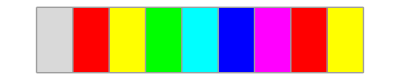
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"ABCDEFGHI"}]
```

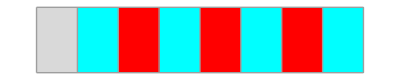
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:

```mathematica
SSSRuleIcon[{"A"->"B",""->"ACDEFGHI"},2] (* Fixed so it doesn't take less than 2 colors, default is 6,  Note: color 0 = LightGray, not part of the cycle if colors are repeated! *)
```

```mathematica
SSSNewRule[{"ABA"->"AAB","A"->"ABA"}]
```

{s[{0,lhsTag$2946_},{1,lhsTag$2947_},{0,lhsTag$2948_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$2946,lhsTag$2947,lhsTag$2948}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$2950_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$2950}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}

Create and initialize a sessie object, look at different fields, use SSSSingleStep, SSSEvolve, SSSDisplay on it:

```mathematica
sss=SSSInitialize[{"ABA"->"AAB","A"->"ABA"}, "A"];
Normal[sss]//Column
```

Net→{}
OutDegreePotential→{3}
OutDegreeRemaining→{3}
OutDegreeActual→{0}
InDegree→{1}
ConnectionList→{{1}→{2,3,4}}
Verdict→OK
RulesUsed→{2}
CellsDeleted→{{1}}
Distance→{0}
MaxColor→6
TagIndex→5
TEvolution→{s[{0,1}],s[{0,2},{1,3},{0,4}]}
Evolution→{A,ABA}
RuleSet→{ABA→AAB,A→ABA}
TRuleSet→{s[{0,lhsTag$2957_},{1,lhsTag$2958_},{0,lhsTag$2959_}]:>(AppendTo[$SSSRulesUsed,1];AppendTo[$SSSConnectionList,{lhsTag$2957,lhsTag$2958,lhsTag$2959}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{0,$SSSTagIndex++},{1,$SSSTagIndex++}]),s[{0,lhsTag$2961_}]:>(AppendTo[$SSSRulesUsed,2];AppendTo[$SSSConnectionList,{lhsTag$2961}→$SSSTagIndex+{0,1,2}];s[{0,$SSSTagIndex++},{1,$SSSTagIndex++},{0,$SSSTagIndex++}]),___:>AppendTo[$SSSRulesUsed,0]}
RuleSetWeight→13
RuleSetLength→10

```mathematica
{sss["TagIndex"],sss["Evolution"]}
```

{5,{A,ABA}}

```mathematica
sss=SSSSingleStep[sss];
{sss["TagIndex"],sss["Evolution"]}
```

{8,{A,ABA,AAB}}

```mathematica
sss=SSSEvolve[sss,50];
sss["Evolution"]
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB,ABAAAAAAAAABBBBBBBB,AABAAAAAAAABBBBBBBB,AAABAAAAAAABBBBBBBB,AAAABAAAAAABBBBBBBB,AAAAABAAAAABBBBBBBB,AAAAAABAAAABBBBBBBB,AAAAAAABAAABBBBBBBB,AAAAAAAABAABBBBBBBB}

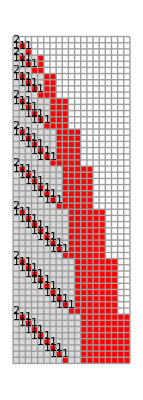


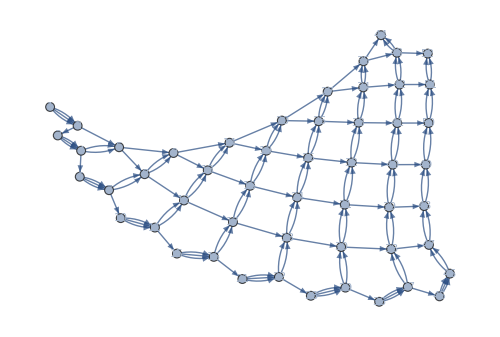
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,NetSize->500]
```

Normal way to create, evolve, and display a sessie object:

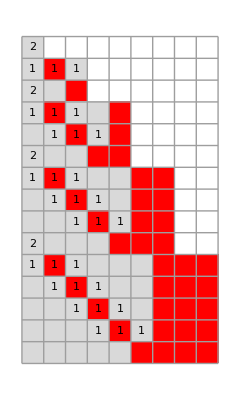
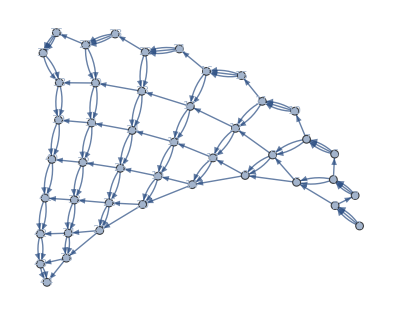
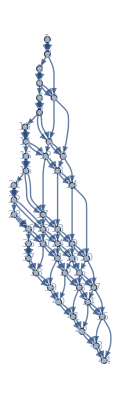
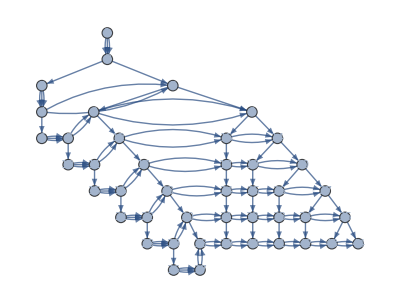
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics--Graphics--Graphics--Graphics3D-

```mathematica
sss=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",44,SSSMax->15,NetMethod->All];
```

Create another SSS without erasing the first one:

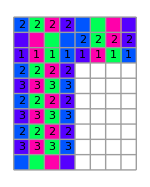
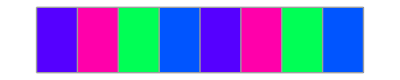
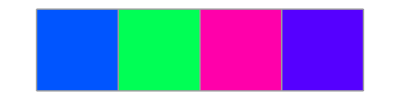
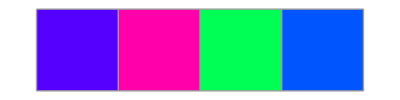
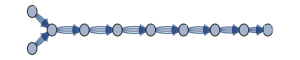
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
mirosessie = SSS[{"ORIMORIM" -> "MIRO", "MIRO" -> "ORIM", "ORIM" -> "MIRO"}, "MIROMIRO", 10, SSSMax -> 10, NetMethod -> GraphPlot, SSSSize->150,NetSize->300];
```

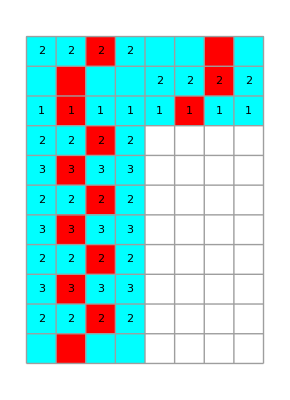
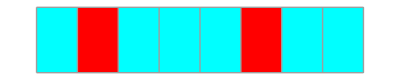
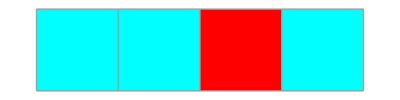
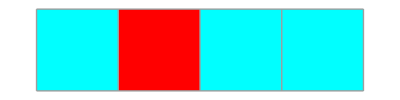
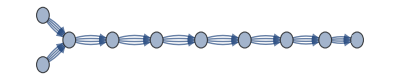
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
AssociateTo[mirosessie, "MaxColor" ->2];  (* colors will now recur, modulo-2: *)
SSSDisplay[mirosessie,NetSize->400]
```

```mathematica
mirosessie["Verdict"]
mirosessie["Evolution"]
mirosessie["MaxColor"]
```

Repeating

{MIROMIRO,ORIMMIRO,ORIMORIM,MIRO,ORIM,MIRO,ORIM,MIRO,ORIM,MIRO,ORIM}

2

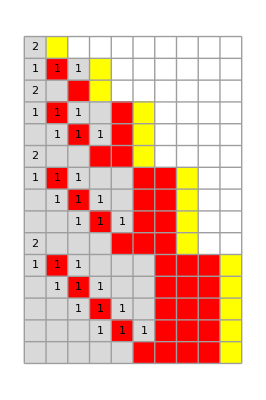
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss2=SSS[{"ABA"->"AAB","A"->"ABA"}, "AC",44,SSSMax->15,NetMethod->GraphPlot];
```

Both sss and sss2 exist independently:

```mathematica
sss["Evolution"]
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB}

```mathematica
sss2["Evolution"]
```

{AC,ABAC,AABC,ABAABC,AABABC,AAABBC,ABAAABBC,AABAABBC,AAABABBC,AAAABBBC,ABAAAABBBC,AABAAABBBC,AAABAABBBC,AAAABABBBC,AAAAABBBBC,ABAAAAABBBBC,AABAAAABBBBC,AAABAAABBBBC,AAAABAABBBBC,AAAAABABBBBC,AAAAAABBBBBC,ABAAAAAABBBBBC,AABAAAAABBBBBC,AAABAAAABBBBBC,AAAABAAABBBBBC,AAAAABAABBBBBC,AAAAAABABBBBBC,AAAAAAABBBBBBC,ABAAAAAAABBBBBBC,AABAAAAAABBBBBBC,AAABAAAAABBBBBBC,AAAABAAAABBBBBBC,AAAAABAAABBBBBBC,AAAAAABAABBBBBBC,AAAAAAABABBBBBBC,AAAAAAAABBBBBBBC,ABAAAAAAAABBBBBBBC,AABAAAAAAABBBBBBBC,AAABAAAAAABBBBBBBC,AAAABAAAAABBBBBBBC,AAAAABAAAABBBBBBBC,AAAAAABAAABBBBBBBC,AAAAAAABAABBBBBBBC,AAAAAAAABABBBBBBBC,AAAAAAAAABBBBBBBBC}

Use SSSInteractiveDisplay to tweak the display options:

```mathematica
SSSInteractiveDisplay[sss]
```

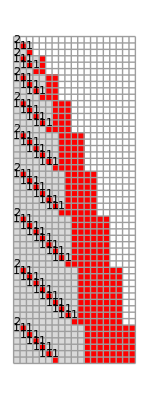
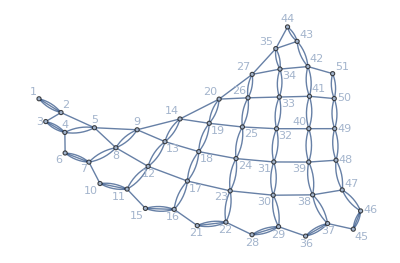
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,Min->1,Max->51,SSSMin->Automatic,SSSMax->Automatic,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->350,NetSize->{Automatic,300},SSSSize->{Automatic,220},IconSize->{Automatic,10.},VertexSize->Automatic,VertexLabels->Automatic,DirectedEdges->False]
```

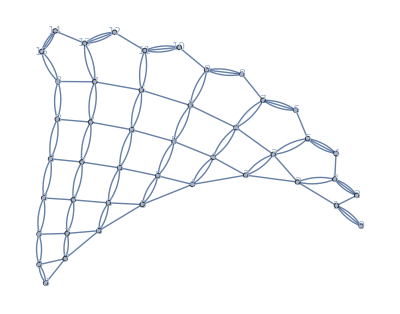

```mathematica
SSSDisplay[sss,Min->1,Max->51,SSSMin->Automatic,SSSMax->Automatic,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot,NoSSS},ImageSize->217.,NetSize->{Automatic,300},SSSSize->{Automatic,220},IconSize->{Automatic,10.},VertexSize->Automatic,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->False]
```

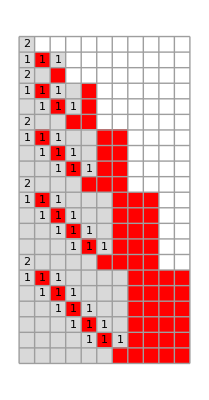
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,Min->1,Max->44,SSSMin->Automatic,SSSMax->21,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->198.,NetSize->{Automatic,342.},SSSSize->{Automatic,220},IconSize->{Automatic,20},VertexSize->Automatic,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->False]
```

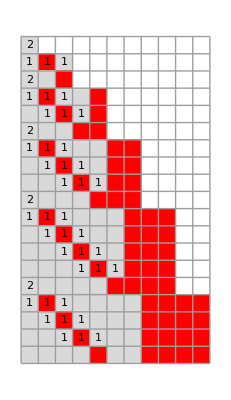
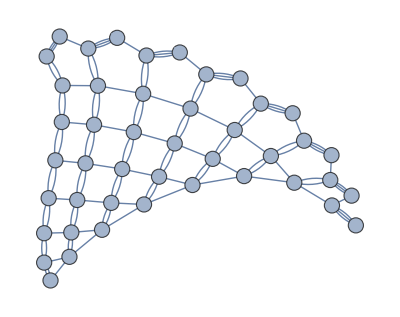
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss,Min->1,Max->44,SSSMin->Automatic,SSSMax->19,NetMin->Automatic,NetMax->Automatic,HighlightMethod->Number,RulePlacement->Bottom,NetMethod->{GraphPlot},ImageSize->209.,NetSize->{Automatic,300},SSSSize->{Automatic,220},IconSize->{Automatic,20},VertexSize->0.8,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->False]
```

Examples of using SSSAnimate:

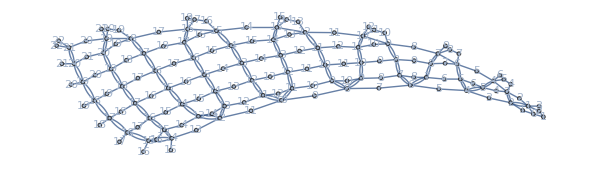

```mathematica
sss3=SSS[{"BAB"->"ABA","A"->"B","B"->"AA"},"BAB",150,NetSize->600,
NetMethod->{GraphPlot,NoSSS},
VertexSize->Automatic,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->False];
```

```mathematica
SSSAnimate[sss3]
```

```mathematica
SSSAnimate[sss3,VertexLabels->"VertexWeight"]
```

```mathematica
SSSInitialState[{"ABA"->"AAB","BB"->"ABA"}]
```

ABABBABB

```mathematica
SSSInitialState[{"ABA"->"AAB","A"->"ABA","CDE"->""}]
```

ABABACDCECDCDECEDCEDEDEC

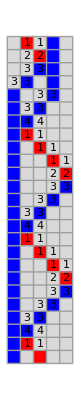


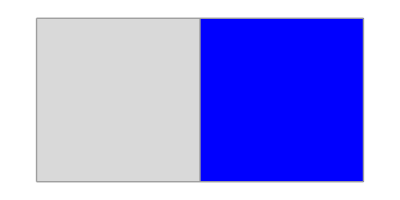
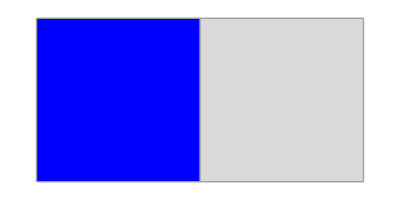
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[2168704802144169502244628730,80,SSSMax->25,NetSize->500,VertexLabels->None];
```

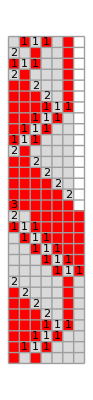
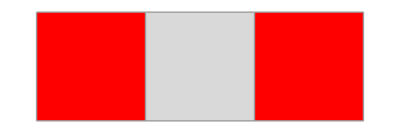
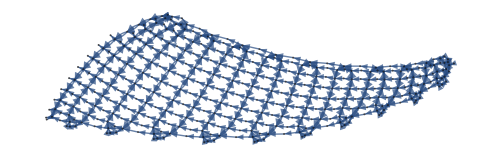
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSS[36660528645,400,SSSMax->30,NetSize->500,VertexLabels->Placed["Name",Tooltip]];
```

Let's look at both the reduced enumeration index and the quinary code of the mirosessie ruleset!  😁

```mathematica
FromReducedRankRuleSet[mirosessie["RuleSet"]]
```

{31724272965613982509673497002743933689002475059552671099609208860239348964268003480421701342935661158978046841164354624000010772998214031024664456344795268591236103093181099442783233154578546344891700474079141153768283931377232895645890131629585061455145478242492675781,444444444444443444444444444444443444444443444444444444344444444444444344444444444444444344444444344444444444424444444444443444444443444444444444444443444444444444442444444444444344444444344444444444444444344444444444444244444444444444344444444444444444344444444344444444444424444444444444434444444444444444434444444434444444444442444444444444344444444344444444444444444344444444444444,{ORIMORIM→MIRO,MIRO→ORIM,ORIM→MIRO}}

Other enumeration examples:

```mathematica
FromReducedRankRuleSet[{"AA"->"BA","AB"->"AA","B"->"A"}]
```

<|Index→236252479,QCode→324323423242,RuleSet→{AA→BA,AB→AA,B→A}|>

```mathematica
FromReducedRankIndex[236252479]
```

<|Index→236252479,QCode→324323423242,RuleSet→{AA→BA,AB→AA,B→A}|>

```mathematica
FromReducedRankQuinaryCode["324323423242"]
```

<|Index→236252479,QCode→324323423242,RuleSet→{AA→BA,AB→AA,B→A}|>

```mathematica
FromReducedRankRuleSet[{"BAB"->"ABA","A"->"B","B"->"AA"}]
```

<|Index→36660528645,QCode→433423432242423,RuleSet→{BAB→ABA,A→B,B→AA}|>

```mathematica
FromReducedRankIndex/@ Range[25]
```

{<|Index→1,QCode→,RuleSet→{A→}|>,<|Index→2,QCode→0,RuleSet→{A→,→A}|>,<|Index→3,QCode→1,RuleSet→{A→,A→}|>,<|Index→4,QCode→2,RuleSet→{A→A}|>,<|Index→5,QCode→3,RuleSet→{AA→}|>,<|Index→6,QCode→4,RuleSet→{B→}|>,<|Index→7,QCode→00,RuleSet→{A→,→A,→,A→}|>,<|Index→8,QCode→01,RuleSet→{A→,→A,→A}|>,<|Index→9,QCode→02,RuleSet→{A→,→A,A→}|>,<|Index→10,QCode→03,RuleSet→{A→,→AA}|>,<|Index→11,QCode→04,RuleSet→{A→,→B}|>,<|Index→12,QCode→10,RuleSet→{A→,A→,→A}|>,<|Index→13,QCode→11,RuleSet→{A→,A→,A→}|>,<|Index→14,QCode→12,RuleSet→{A→,A→A}|>,<|Index→15,QCode→13,RuleSet→{A→,AA→}|>,<|Index→16,QCode→14,RuleSet→{A→,B→}|>,<|Index→17,QCode→20,RuleSet→{A→A,→,A→}|>,<|Index→18,QCode→21,RuleSet→{A→A,→A}|>,<|Index→19,QCode→22,RuleSet→{A→A,A→}|>,<|Index→20,QCode→23,RuleSet→{A→AA}|>,<|Index→21,QCode→24,RuleSet→{A→B}|>,<|Index→22,QCode→30,RuleSet→{AA→,→A}|>,<|Index→23,QCode→31,RuleSet→{AA→,A→}|>,<|Index→24,QCode→32,RuleSet→{AA→A}|>,<|Index→25,QCode→33,RuleSet→{AAA→}|>}

```mathematica
Grid[
Prepend[
Values[FromReducedRankIndex[#]]&/@ Range[50],
{"index","q-code","ruleset"}],
Alignment->Left,Dividers->{None,{False,True}}]
```

index | q-code | ruleset
1 |  | {A→}
2 | 0 | {A→,→A}
3 | 1 | {A→,A→}
4 | 2 | {A→A}
5 | 3 | {AA→}
6 | 4 | {B→}
7 | 00 | {A→,→A,→,A→}
8 | 01 | {A→,→A,→A}
9 | 02 | {A→,→A,A→}
10 | 03 | {A→,→AA}
11 | 04 | {A→,→B}
12 | 10 | {A→,A→,→A}
13 | 11 | {A→,A→,A→}
14 | 12 | {A→,A→A}
15 | 13 | {A→,AA→}
16 | 14 | {A→,B→}
17 | 20 | {A→A,→,A→}
18 | 21 | {A→A,→A}
19 | 22 | {A→A,A→}
20 | 23 | {A→AA}
21 | 24 | {A→B}
22 | 30 | {AA→,→A}
23 | 31 | {AA→,A→}
24 | 32 | {AA→A}
25 | 33 | {AAA→}
26 | 34 | {AB→}
27 | 40 | {B→,→A}
28 | 41 | {B→,A→}
29 | 42 | {B→A}
30 | 43 | {BA→}
31 | 44 | {C→}
32 | 000 | {A→,→A,→,A→,→A}
33 | 001 | {A→,→A,→,A→,A→}
34 | 002 | {A→,→A,→,A→A}
35 | 003 | {A→,→A,→,AA→}
36 | 004 | {A→,→A,→,B→}
37 | 010 | {A→,→A,→A,→,A→}
38 | 011 | {A→,→A,→A,→A}
39 | 012 | {A→,→A,→A,A→}
40 | 013 | {A→,→A,→AA}
41 | 014 | {A→,→A,→B}
42 | 020 | {A→,→A,A→,→A}
43 | 021 | {A→,→A,A→,A→}
44 | 022 | {A→,→A,A→A}
45 | 023 | {A→,→A,AA→}
46 | 024 | {A→,→A,B→}
47 | 030 | {A→,→AA,→,A→}
48 | 031 | {A→,→AA,→A}
49 | 032 | {A→,→AA,A→}
50 | 033 | {A→,→AAA}

```mathematica
FromReducedRankRuleSet[{"AA"->"BA","AB"->"AA","B"->"AA"}]
```

<|Index→1181262395,QCode→3243234232423,RuleSet→{AA→BA,AB→AA,B→AA}|>

```mathematica
Grid[Prepend[Values[FromReducedRankIndex[#]]&/@ (1181262395+Range[0,25]),
{"index","q-code","ruleset"}],Alignment->Left,Dividers->{None,{False,True}}]
```

index | q-code | ruleset
1181262395 | 3243234232423 | {AA→BA,AB→AA,B→AA}
1181262396 | 3243234232424 | {AA→BA,AB→AA,B→B}
1181262397 | 3243234232430 | {AA→BA,AB→AA,BA→,→A}
1181262398 | 3243234232431 | {AA→BA,AB→AA,BA→,A→}
1181262399 | 3243234232432 | {AA→BA,AB→AA,BA→A}
1181262400 | 3243234232433 | {AA→BA,AB→AA,BAA→}
1181262401 | 3243234232434 | {AA→BA,AB→AA,BB→}
1181262402 | 3243234232440 | {AA→BA,AB→AA,C→,→A}
1181262403 | 3243234232441 | {AA→BA,AB→AA,C→,A→}
1181262404 | 3243234232442 | {AA→BA,AB→AA,C→A}
1181262405 | 3243234232443 | {AA→BA,AB→AA,CA→}
1181262406 | 3243234232444 | {AA→BA,AB→AA,D→}
1181262407 | 3243234233000 | {AA→BA,AB→AAA,→,A→,→A,→,A→}
1181262408 | 3243234233001 | {AA→BA,AB→AAA,→,A→,→A,→A}
1181262409 | 3243234233002 | {AA→BA,AB→AAA,→,A→,→A,A→}
1181262410 | 3243234233003 | {AA→BA,AB→AAA,→,A→,→AA}
1181262411 | 3243234233004 | {AA→BA,AB→AAA,→,A→,→B}
1181262412 | 3243234233010 | {AA→BA,AB→AAA,→,A→,A→,→A}
1181262413 | 3243234233011 | {AA→BA,AB→AAA,→,A→,A→,A→}
1181262414 | 3243234233012 | {AA→BA,AB→AAA,→,A→,A→A}
1181262415 | 3243234233013 | {AA→BA,AB→AAA,→,A→,AA→}
1181262416 | 3243234233014 | {AA→BA,AB→AAA,→,A→,B→}
1181262417 | 3243234233020 | {AA→BA,AB→AAA,→,A→A,→,A→}
1181262418 | 3243234233021 | {AA→BA,AB→AAA,→,A→A,→A}
1181262419 | 3243234233022 | {AA→BA,AB→AAA,→,A→A,A→}
1181262420 | 3243234233023 | {AA→BA,AB→AAA,→,A→AA}

## Ruleset Tests: Explanations & Examples

Now all Test... functions expect an argument of the Association with Keys {"Index", "QCode", "RuleSet"}, and return {} (if not applicable) or resolution ruleset object.

### TestForConflictingRules

A pair of conflicting rules occurs when two rules in the ruleset have the same left-hand side, or more generally, when the left-hand side of one rule is a substring of the left-hand side of a later rule. For example, consider the ruleset {"ABA"→"AAB", "ABA"→"", "A"→"ABA"} (# 158 448 842 380 in the RSS list, quinary code = 3432334234312343_5).  Here, rule 2 conflicts with rule 1, and will never be used.

Check rule by rule, starting with j = 2, see whether rule j conflicts with any previous rules.  If so, find the match that ends earliest in lhs j, and let rule i be the one that gave this match.  Stop on first match.

In the reduced enumeration of SSS rulesets we can "long-jump" past all rulesets sharing the initial part of the ruleset, including the conflicting rules.  (The resolution ruleset is the first that does not have the same problem:  it may have the first rule but does not have the second.)

Christen has convinced me that after every long-jump of this type, there will be a series of additional jumps due to creation rules, ending with the ruleset that has tailweight of appended As.  This means longer long-jumps!  Unfortunately there appears to be a different goal ruleset depending on whether the original match in the conflicting rules’ lhs is the empty string or something else, and if something else we still have two sub-cases, depending on whether the tailweight is 1 or more.  Rather than separately testing for these subcases, we will simply repeat the TestForConflictingRules, and the second test will always match an empty string, catching a (different) conflicting rules situation with a non-final creation rule.

Note: in an accelerated iteration through the Reduced SS enumeration, after every successful long-jump, we now plan to immediately perform a TestForConflictingRules!

Seeking an operation on the quinary codes justifies treating only two (2) cases:  (1) a conflicting rules case with a non-empty match,  (2) a conflicting rules case with an empty match string, “” (triggered by a ‘0’ or ‘1’ in the quinary code).  Only in the second case will we jump past the additional mini-jumps due to the creation rule.  For the first case, we actually set up a creation rule for the next application of the test to take care of, but it is a different problem.  This seems like extra work, but it is a minimalist strategy, in both cases we jump past the immediate problem, in the first we know that there will immediately be another problem, but it will be resolved without special treatment in one additional step.

non-creation case:  replace last tailweight digits of qcode by ‘4000...0’.  (Equivalent to:  keep all rules up to j-1, keep lhs of rule j up to but not including last character of match position,increment final character of match, use "" as rhs. Now spread out remaining weight as much as possible by filling up the quinary digits with 0s.  (Each 0 adds "", "", "A" to the ruleset.)

creation case:  replace last tailweight digits of the qcode by ‘3’s.  (Equivalent to:  keep rules up to j-2, append tailweight string of As to the rhs of rule j-1, stop)

Examples of RuleSet Tests:

```mathematica
FromReducedRankQuinaryCode["3432334234312343"]
TestForConflictingRules[%]
```

<|Index→158448842380,QCode→3432334234312343,RuleSet→{ABA→AAB,ABA→,A→ABA}|>

<|Index→158448843907,QCode→3432334234340000,RuleSet→{ABA→AAB,ABB→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["24344234244"]
TestForConflictingRules[%]
```

<|Index→41106356,QCode→24344234244,RuleSet→{A→BC,AB→C}|>

<|Index→41106407,QCode→24344240000,RuleSet→{A→BC,B→,→A,→,A→,→A,→,A→}|>

```mathematica
Grid[
Prepend[
Values[FromReducedRankIndex[#]]&/@ (41106356+Range[0,51]),
{"index","q-code","ruleset"}],
Alignment->Left,Dividers->{None,{False,True}}]
```

index | q-code | ruleset
41106356 | 24344234244 | {A→BC,AB→C}
41106357 | 24344234300 | {A→BC,ABA→,→A,→,A→}
41106358 | 24344234301 | {A→BC,ABA→,→A,→A}
41106359 | 24344234302 | {A→BC,ABA→,→A,A→}
41106360 | 24344234303 | {A→BC,ABA→,→AA}
41106361 | 24344234304 | {A→BC,ABA→,→B}
41106362 | 24344234310 | {A→BC,ABA→,A→,→A}
41106363 | 24344234311 | {A→BC,ABA→,A→,A→}
41106364 | 24344234312 | {A→BC,ABA→,A→A}
41106365 | 24344234313 | {A→BC,ABA→,AA→}
41106366 | 24344234314 | {A→BC,ABA→,B→}
41106367 | 24344234320 | {A→BC,ABA→A,→,A→}
41106368 | 24344234321 | {A→BC,ABA→A,→A}
41106369 | 24344234322 | {A→BC,ABA→A,A→}
41106370 | 24344234323 | {A→BC,ABA→AA}
41106371 | 24344234324 | {A→BC,ABA→B}
41106372 | 24344234330 | {A→BC,ABAA→,→A}
41106373 | 24344234331 | {A→BC,ABAA→,A→}
41106374 | 24344234332 | {A→BC,ABAA→A}
41106375 | 24344234333 | {A→BC,ABAAA→}
41106376 | 24344234334 | {A→BC,ABAB→}
41106377 | 24344234340 | {A→BC,ABB→,→A}
41106378 | 24344234341 | {A→BC,ABB→,A→}
41106379 | 24344234342 | {A→BC,ABB→A}
41106380 | 24344234343 | {A→BC,ABBA→}
41106381 | 24344234344 | {A→BC,ABC→}
41106382 | 24344234400 | {A→BC,AC→,→A,→,A→}
41106383 | 24344234401 | {A→BC,AC→,→A,→A}
41106384 | 24344234402 | {A→BC,AC→,→A,A→}
41106385 | 24344234403 | {A→BC,AC→,→AA}
41106386 | 24344234404 | {A→BC,AC→,→B}
41106387 | 24344234410 | {A→BC,AC→,A→,→A}
41106388 | 24344234411 | {A→BC,AC→,A→,A→}
41106389 | 24344234412 | {A→BC,AC→,A→A}
41106390 | 24344234413 | {A→BC,AC→,AA→}
41106391 | 24344234414 | {A→BC,AC→,B→}
41106392 | 24344234420 | {A→BC,AC→A,→,A→}
41106393 | 24344234421 | {A→BC,AC→A,→A}
41106394 | 24344234422 | {A→BC,AC→A,A→}
41106395 | 24344234423 | {A→BC,AC→AA}
41106396 | 24344234424 | {A→BC,AC→B}
41106397 | 24344234430 | {A→BC,ACA→,→A}
41106398 | 24344234431 | {A→BC,ACA→,A→}
41106399 | 24344234432 | {A→BC,ACA→A}
41106400 | 24344234433 | {A→BC,ACAA→}
41106401 | 24344234434 | {A→BC,ACB→}
41106402 | 24344234440 | {A→BC,AD→,→A}
41106403 | 24344234441 | {A→BC,AD→,A→}
41106404 | 24344234442 | {A→BC,AD→A}
41106405 | 24344234443 | {A→BC,ADA→}
41106406 | 24344234444 | {A→BC,AE→}
41106407 | 24344240000 | {A→BC,B→,→A,→,A→,→A,→,A→}

```mathematica
FromReducedRankQuinaryCode["434422434424224"]
TestForConflictingRules[%]
```

<|Index→36902752596,QCode→434422434424224,RuleSet→{BC→A,BC→B,A→B}|>

<|Index→36902753282,QCode→434422434440000,RuleSet→{BC→A,BD→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["24144124234"]
TestForConflictingRules[%]
```

<|Index→40321351,QCode→24144124234,RuleSet→{A→B,→C,→A,B→AB}|>

<|Index→40328125,QCode→24144333333,RuleSet→{A→B,→CAAAAAA}|>

```mathematica
FromReducedRankQuinaryCode["2414434124234"]
TestForConflictingRules[%]
```

<|Index→1008211976,QCode→2414434124234,RuleSet→{A→B,→CB,→A,B→AB}|>

<|Index→1008218750,QCode→2414434333333,RuleSet→{A→B,→CBAAAAAA}|>

```mathematica
FromReducedRankIndex[321351]
TestForConflictingRules[%]
```

<|Index→321351,QCode→24124234,RuleSet→{A→B,→A,B→AB}|>

<|Index→321875,QCode→24133333,RuleSet→{A→B,→AAAAAA}|>

```mathematica
FromReducedRankIndex[8065101]
TestForConflictingRules[%]
```

<|Index→8065101,QCode→2414424234,RuleSet→{A→B,→C,B→AB}|>

<|Index→8065625,QCode→2414433333,RuleSet→{A→B,→CAAAAA}|>

```mathematica
FromReducedRankIndex[40321351]
TestForConflictingRules[%]
```

<|Index→40321351,QCode→24144124234,RuleSet→{A→B,→C,→A,B→AB}|>

<|Index→40328125,QCode→24144333333,RuleSet→{A→B,→CAAAAAA}|>

```mathematica
FromReducedRankIndex[40328125]
TestForConflictingRules[%]
```

<|Index→40328125,QCode→24144333333,RuleSet→{A→B,→CAAAAAA}|>

{}

```mathematica
FromReducedRankIndex[13267]
TestForConflictingRules[%]
```

<|Index→13267,QCode→244420,RuleSet→{A→D,A→,→A}|>

<|Index→13271,QCode→244424,RuleSet→{A→D,B→}|>

Examples from JCS paper:

```mathematica
FromReducedRankQuinaryCode["3432334234312343"]
TestForConflictingRules[%]
```

<|Index→158448842380,QCode→3432334234312343,RuleSet→{ABA→AAB,ABA→,A→ABA}|>

<|Index→158448843907,QCode→3432334234340000,RuleSet→{ABA→AAB,ABB→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["24344234244"]
TestForConflictingRules[%]
```

<|Index→41106356,QCode→24344234244,RuleSet→{A→BC,AB→C}|>

<|Index→41106407,QCode→24344240000,RuleSet→{A→BC,B→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["434422434424224"]
TestForConflictingRules[%]
```

<|Index→36902752596,QCode→434422434424224,RuleSet→{BC→A,BC→B,A→B}|>

<|Index→36902753282,QCode→434422434440000,RuleSet→{BC→A,BD→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["24144124234"]
TestForConflictingRules[%]
```

<|Index→40321351,QCode→24144124234,RuleSet→{A→B,→C,→A,B→AB}|>

<|Index→40328125,QCode→24144333333,RuleSet→{A→B,→CAAAAAA}|>

```mathematica
FromReducedRankQuinaryCode["2414434124234"]
TestForConflictingRules[%]
```

<|Index→1008211976,QCode→2414434124234,RuleSet→{A→B,→CB,→A,B→AB}|>

<|Index→1008218750,QCode→2414434333333,RuleSet→{A→B,→CBAAAAAA}|>

```mathematica
FromReducedRankQuinaryCode["2404234"]
TestForConflictingRules[%]
```

<|Index→63851,QCode→2404234,RuleSet→{A→B,→,B→AB}|>

<|Index→64375,QCode→2413333,RuleSet→{A→B,→AAAAA}|>

### TestForIdentityRule, TestForNonSoloIdentityRule

An identity rule occurs when the left-hand side of a rule is identical to the right-hand side of that same rule. A ruleset containing an identity rule and at least one other rule can be discarded, whether or not the identity rule is ever executed. For example, consider the ruleset {"A"→"CC", "B"→"B", "C"→"A"} (# 5 178 059 904 in RSS list, quinary code = 24434424242442_5). If the second rule is never executed, the behavior of the ruleset is equivalent to a simpler, previously considered one, without the identity rule: {"A"→"CC", "C"→"A"} (# 8 284 904, quinary code = 2443442442_5).  On the other hand, if the identity rule is executed once, the enumeration will go into an infinite loop of "B"→"B" and any later rules will never be executed afterwards.

TestForIdentityRule[rs] tests for any identity rule anywhere in the ruleset, TestForNonSoloIdentityRule tests for a ruleset containing an identity rule and at least one other (and is therefore discardable).  A solo identity rule is not a problem, but it will generate a simple single- or multiple-stranded chain -- depending on the length of the string in the rule.  Therefore at this point we may optionally discard out of hand all rulesets containing an identity rule, IF solo identity rules are considered separately.

The procedure for finding the resolution to an identity rule situation depends on whether it is a ""→"" rule or not.  In both cases we need to know w, the weight of the rules following the identity rule.  A "nothing to nothing" rule is created by a 0 in the quinary code (the instruction to end the current string, insert two empty strings, and start a new string with "A").  In this case, resolution is achieved by replacing the last w quinary digits by '1000...0'.  The '1' changes the "nothing to nothing" rule to a "nothing to something", and filling in with '0' digits ensures that no cases will be left out.  On the other hand, to jump past any other type of identity rule situation, we simply have to append an "A" to the rhs of the identity rule, which can be done by by replacing the last w quinary digits by '3000...0'.

TestForNonSoloIdentityRule does a preliminary check for singleton rulesets, returning {} if applicable, and only tests for identity rules otherwise.  This version would be used if singleton cases are of interest.  For example, the first single strand 1-d network is created by the ruleset {"A"→"A"}, the first double strand 1-d network by the ruleset {"AA"→"AA}.

```mathematica
TestForIdentityRule@FromReducedRankRuleSet@{"A"->"A"}
```

<|Index→5,QCode→3,RuleSet→{AA→}|>

```mathematica
TestForNonSoloIdentityRule@FromReducedRankRuleSet@{"A"->"A"}
```

{}

```mathematica
FromReducedRankRuleSet@{"A"->"BB","C"->"C","AA"->"B",""->"A"}
```

<|Index→25676111853,QCode→243424424423241,RuleSet→{A→BB,C→C,AA→B,→A}|>

```mathematica
TestForIdentityRule@%
```

<|Index→25676112032,QCode→243424424430000,RuleSet→{A→BB,C→CA,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankRuleSet@{"A"->"BB","C"->"C"}
TestForIdentityRule@%
```

<|Index→8216356,QCode→2434244244,RuleSet→{A→BB,C→C}|>

<|Index→8216357,QCode→2434244300,RuleSet→{A→BB,CA→,→A,→,A→}|>

```mathematica
FromReducedRankRuleSet@{"A"->"BB",""->"","B"->"A"}
TestForIdentityRule@%
```

<|Index→65679,QCode→2434042,RuleSet→{A→BB,→,B→A}|>

<|Index→65682,QCode→2434100,RuleSet→{A→BB,→A,→,A→,→A}|>

```mathematica
Grid[Prepend[Values[FromReducedRankIndex[#]]&/@ Range[65657-1,65682],
{"index","q-code","ruleset"}],Alignment->Left,Dividers->{None,{False,True}},Background->{Automatic,{3->LightPink,-4->LightPurple,-1->LightGreen}}]
```

index | q-code | ruleset
65656 | 2433444 | {A→BAD}
65657 | 2434000 | {A→BB,→,A→,→A,→,A→}
65658 | 2434001 | {A→BB,→,A→,→A,→A}
65659 | 2434002 | {A→BB,→,A→,→A,A→}
65660 | 2434003 | {A→BB,→,A→,→AA}
65661 | 2434004 | {A→BB,→,A→,→B}
65662 | 2434010 | {A→BB,→,A→,A→,→A}
65663 | 2434011 | {A→BB,→,A→,A→,A→}
65664 | 2434012 | {A→BB,→,A→,A→A}
65665 | 2434013 | {A→BB,→,A→,AA→}
65666 | 2434014 | {A→BB,→,A→,B→}
65667 | 2434020 | {A→BB,→,A→A,→,A→}
65668 | 2434021 | {A→BB,→,A→A,→A}
65669 | 2434022 | {A→BB,→,A→A,A→}
65670 | 2434023 | {A→BB,→,A→AA}
65671 | 2434024 | {A→BB,→,A→B}
65672 | 2434030 | {A→BB,→,AA→,→A}
65673 | 2434031 | {A→BB,→,AA→,A→}
65674 | 2434032 | {A→BB,→,AA→A}
65675 | 2434033 | {A→BB,→,AAA→}
65676 | 2434034 | {A→BB,→,AB→}
65677 | 2434040 | {A→BB,→,B→,→A}
65678 | 2434041 | {A→BB,→,B→,A→}
65679 | 2434042 | {A→BB,→,B→A}
65680 | 2434043 | {A→BB,→,BA→}
65681 | 2434044 | {A→BB,→,C→}
65682 | 2434100 | {A→BB,→A,→,A→,→A}

Examples from JCS paper:

```mathematica
FromReducedRankQuinaryCode["442222424344"]
TestForIdentityRule@%
```

<|Index→300299506,QCode→442222424344,RuleSet→{C→A,A→A,B→BC}|>

<|Index→300300782,QCode→442223000000,RuleSet→{C→A,A→AA,→,A→,→A,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankQuinaryCode["4234234323432243"]
TestForIdentityRule@%
```

<|Index→177199143605,QCode→4234234323432243,RuleSet→{B→AB,ABA→ABA,A→BA}|>

<|Index→177199143657,QCode→4234234323433000,RuleSet→{B→AB,ABA→ABAA,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankQuinaryCode["434424344224242344"]
TestForIdentityRule@%
```

<|Index→4613292513006,QCode→434424344224242344,RuleSet→{BC→BC,A→B,B→AC}|>

<|Index→4613292675782,QCode→434424344300000000,RuleSet→{BC→BCA,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankQuinaryCode["2404234"]
TestForIdentityRule@%
```

<|Index→63851,QCode→2404234,RuleSet→{A→B,→,B→AB}|>

<|Index→63907,QCode→2410000,RuleSet→{A→B,→A,→,A→,→A,→,A→,→A}|>

### TestForRenamedRuleSet

If the characters used in the strings of the ruleset are permuted or replaced by other characters, the SSS will look the same up to a permutation of colors, and the causal network will be identical.  Such cases can be identified without generating the SSS, as follows:

Examine the characters of all the strings of the ruleset in order, one character at a time.  The first character must be “A” (else renaming could make it so -- a previously seen case), the first character that is not an “A” must be a “B”, and the first that is not “A” or “B” must be “C”, etc.  As soon as an offending  character is found, take the total weight of all further characters, and replace that number of quinary code digits by ‘4’. This gives the quinary code of the last ruleset having a too-large character (now with maximal weight) at the problem position and same pre-problem (sub)strings, so this is the last ruleset that can safely be discarded in a long-jump.  (The resolution ruleset is the next in the enumeration, found by incrementing the RSS index by 1.)

Return resolution ruleset object, as usual.  If the test is negative, return {} as usual.

Important note:  Although the renamed ruleset may actually have a greater weight than the original version, this jump is safe and will allow us to skip all but one version of each ruleset (up to a permutation of the characters themselves).  It is true that we may have to wait until later in the enumeration to find some interesting case, since the renaming process preserves ruleset length, not ruleset weight.  But the advantage of being able to jump over huge intervals is too good to be missed, and we can always later find the canonical representative, the lowest index of the possible renamings of any interesting case, using the function ToCanonical.

```mathematica
FromReducedRankQuinaryCode["24242"]
TestForRenamedRuleSet[%]
```

<|Index→2604,QCode→24242,RuleSet→{A→B,B→A}|>

{}

There was no problem.

```mathematica
FromReducedRankQuinaryCode["42224"]
TestForRenamedRuleSet[%]
```

<|Index→3596,QCode→42224,RuleSet→{B→A,A→B}|>

<|Index→3907,QCode→000000,RuleSet→{A→,→A,→,A→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankIndex@3906
```

<|Index→3906,QCode→44444,RuleSet→{F→}|>

Last problem ruleset had weight 6 (5 quinary digits), resolution is in the next weight class.

```mathematica
FromReducedRankQuinaryCode["244424442"]
TestForRenamedRuleSet[%]
```

<|Index→1658904,QCode→244424442,RuleSet→{A→D,D→A}|>

<|Index→1660157,QCode→300000000,RuleSet→{AA→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankIndex@1660156
```

<|Index→1660156,QCode→244444444,RuleSet→{A→I}|>

Resolution involved appending an "A".

```mathematica
FromReducedRankQuinaryCode["34244422424"]
TestForRenamedRuleSet[%]
```

<|Index→50486771,QCode→34244422424,RuleSet→{AB→D,A→B,B→}|>

<|Index→50488282,QCode→34300000000,RuleSet→{ABA→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankIndex@50488281
```

<|Index→50488281,QCode→34244444444,RuleSet→{AB→I}|>

Resolution involved appending an "A".

```mathematica
FromReducedRankQuinaryCode["2343244234344443"]
TestForRenamedRuleSet[%]
```

<|Index→123253532030,QCode→2343244234344443,RuleSet→{A→ABA,C→ABEA}|>

<|Index→123253532032,QCode→2343244234400000,RuleSet→{A→ABA,C→AC,→,A→,→A,→,A→,→A,→,A→}|>

```mathematica
FromReducedRankIndex@123253532031
```

<|Index→123253532031,QCode→2343244234344444,RuleSet→{A→ABA,C→ABF}|>

Resolution involved incrementing the "B" in the rhs of rule 2.

```mathematica
FromReducedRankQuinaryCode["2343244234344444"]
TestForRenamedRuleSet[%]
```

<|Index→123253532031,QCode→2343244234344444,RuleSet→{A→ABA,C→ABF}|>

<|Index→123253532032,QCode→2343244234400000,RuleSet→{A→ABA,C→AC,→,A→,→A,→,A→,→A,→,A→}|>

Same resolution if we apply the test to the last problem case above.

### TestForInitialSubstringRule, TestForNonSoloInitialProperSubstringRule

TestForInitialSubstringRule[rs] tests whether a ruleset begins with any substring rule: a rule in which a string is replaced by a string of which it is a substring, returning either the empty set (if first rule is not a substring rule) or (if applicable) the resolution ruleset to long-jump over the current subsequence of the enumeration that has the same problem.  If not solo, such a ruleset is effectively equivalent to one or the other of two lower-weight, previously seen rulesets:  omitting the problem substring rule, or omitting all rules that follow it.

In the case of a solo substring rule, such a ruleset produces the same causal network (although not the same SSS) as a simpler solo identity rule case:  e.g., {A→ABC} has the same causal network as {A→A}.  In any case initial substring rulesets can be discarded.  Note: as currently implemented, TestForInitialSubstringRule will rule out solo substring and solo identity rules.  If these are explicitly desired, either use TestForNonSoloInitialProperSubstringRule instead, or treat the desired cases separately.  (Easily done: an identity rule of lhs string length n creates a chain where each node is linked n times to the subsequent node.  It's enough to consider {A→A}, {AA→AA}, {AAA→AAA}, ….  The choice of characters will not affect the network.

Note:  initial creation rules (although they appear only in the GSS enumeration, not the reduced enumeration), are a special case of initial substring rules, but they produce no causal networks: only cell creation, no destruction, and therefore no links.

```mathematica
FromReducedRankQuinaryCode["2433442424424424"]
TestForInitialSubstringRule[%]
```

<|Index→128230799521,QCode→2433442424424424,RuleSet→{A→BAC,B→C,C→B}|>

<|Index→128234863282,QCode→2434000000000000,RuleSet→{A→BB,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankQuinaryCode["342343442442"]
TestForInitialSubstringRule[%]
```

<|Index→252034904,QCode→342343442442,RuleSet→{AB→ABC,C→A}|>

<|Index→252035157,QCode→342344000000,RuleSet→{AB→AC,→,A→,→A,→,A→,→A,→,A→,→A}|>

```mathematica
FromReducedRankQuinaryCode["242342343442442"]
TestForInitialSubstringRule[%]
```

<|Index→25398519279,QCode→242342343442442,RuleSet→{A→B,AB→ABC,C→A}|>

{}

Not an initial substring case.

```mathematica
FromReducedRankRuleSet[{"AB"->"ABC"}]
```

<|Index→403256,QCode→34234344,RuleSet→{AB→ABC}|>

```mathematica
FromReducedRankQuinaryCode["34234344"]
TestForInitialSubstringRule[%]
TestForNonSoloInitialProperSubstringRule[%%]
```

<|Index→403256,QCode→34234344,RuleSet→{AB→ABC}|>

<|Index→403257,QCode→34234400,RuleSet→{AB→AC,→,A→,→A}|>

{}

```mathematica
FromReducedRankQuinaryCode["342342"]
TestForInitialSubstringRule[%]
TestForNonSoloInitialProperSubstringRule[%%]
```

<|Index→16129,QCode→342342,RuleSet→{AB→AB,A→}|>

<|Index→16131,QCode→342344,RuleSet→{AB→AC}|>

{}

Not an non-solo initial proper substring case.

### TestForShorteningRuleSet

If all of the rules shorten the state string, the SSS must inevitably die out when the rules cease to be applied, either when the state string has shrunk to zero length or possibly before.  In addition, if none of the rules lengthen the state string, and at least one of them shortens it, that shortening rule will eventually cease to be applied, and therefore the SSS reduces to a previously considered simpler one.  In either case we designate such a ruleset as a shortening ruleset, and it may be discarded without generating the SSS, although no long-jumps can be justified.  The following function tests whether this situation occurs:

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->""}
```

<|Index→2,QCode→0,RuleSet→{A→,→A}|>

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->"A"}
```

{}

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->"B","B"->"A"}
```

{}

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->"B","B"->""}
```

<|Index→522,QCode→2430,RuleSet→{A→BA,→,A→}|>

```mathematica
TestForShorteningRuleSet@FromReducedRankRuleSet@{"A"->"BC","B"->""}
```

{}

### TestForUnbalancedRuleSet

If any letter appears in one or more left-hand side rule strings but not in any right-hand side rule string, or vice versa, we call the ruleset unbalanced.  The behavior of such a ruleset will always duplicate that of some simpler ruleset.  If the extra letter is on a LHS, the rule concerned can at most be executed a finite number of times until all initial occurrences of the letter are “used up”.  On the other hand, if the extra letter occurs in the RHS of some rule, additional unmoveable instances of the letter are produced whenever the rule is executed.  If the rule stops being used, the future behavior of the ruleset simplifies to that of a simpler ruleset, else it creates an infinite number of “barriers” in the state string, separating portions that are thereafter mutually unreachable.  Even two such regions cannot be active indefinitely, since our rulesets are finite.  From some point on the activity will be limited to one of the regions, and again the behavior becomes that of a simpler ruleset.  (Note:  TRY TO VERIFY THIS!)  These considerations allow the exclusion of unbalanced rulesets without the need for stepping through their evolution.

```mathematica
TestForUnbalancedRuleSet@FromReducedRankRuleSet@{"A"->"B","B"->"A","A"->"C"}
```

<|Index→1627357,QCode→242422300,RuleSet→{A→B,B→A,AA→,→A,→,A→}|>

```mathematica
FromReducedRankIndex /@ (1627357+Range[-1,0])
```

{<|Index→1627356,QCode→242422244,RuleSet→{A→B,B→A,A→C}|>,<|Index→1627357,QCode→242422300,RuleSet→{A→B,B→A,AA→,→A,→,A→}|>}

### Example of an accelerated iteration loop

```mathematica
casesTreated=0;
rs=FromReducedRankIndex[1];  (* or other desired starting point in the enumeration *)
While[rs["Index"]<10^4,                                                           (* or some large number, stopping point *)
ans=TestForConflictingRules[rs];
If[Length[ans]>0,rs=ans;Continue[]];  (* if applicable, long-jump *)

ans=TestForNonSoloIdentityRule[rs];
If[Length[ans]>0,rs=ans;Continue[]];

ans=TestForRenamedRuleSet[rs];
If[Length[ans]>0,rs=ans;Continue[]];

ans=TestForNonSoloInitialProperSubstringRule[rs];
If[Length[ans]>0,rs=ans;Continue[]];

(* tests that don't actually provoke long-jumps: *)

ans=TestForUnbalancedRuleSet[rs];
If[Length[ans]>0,rs=ans;Continue[]];

ans=TestForShorteningRuleSet[rs];
If[Length[ans]>0,rs=ans;Continue[]];

(* if none of the rules above applied, do something with rs here *) 

(* for example, just list the rulesets left to consider, counting them as we go *)
Print["# treated: ",++casesTreated," (",Round[100casesTreated/rs["Index"],.1],"%), n = ",rs["Index"], ": ",Subscript[rs["QCode"],5], ", ",rs["RuleSet"]];

(* finally, increment and loop *)
rs=FromReducedRankIndex[rs["Index"]+1]
]
```

# treated: 1 (50.%), n = 2: 0_5, {A→,→A}

# treated: 2 (50.%), n = 4: 2_5, {A→A}

# treated: 3 (30.%), n = 10: 03_5, {A→,→AA}

# treated: 4 (20.%), n = 20: 23_5, {A→AA}

# treated: 5 (22.7%), n = 22: 30_5, {AA→,→A}

# treated: 6 (12.%), n = 50: 033_5, {A→,→AAA}

# treated: 7 (6.4%), n = 110: 303_5, {AA→,→AA}

# treated: 8 (7.1%), n = 112: 310_5, {AA→,A→,→A}

# treated: 9 (7.6%), n = 118: 321_5, {AA→A,→A}

# treated: 10 (8.3%), n = 120: 323_5, {AA→AA}

# treated: 11 (9.%), n = 122: 330_5, {AAA→,→A}

# treated: 12 (4.8%), n = 250: 0333_5, {A→,→AAAA}

# treated: 13 (2.4%), n = 550: 3033_5, {AA→,→AAA}

# treated: 14 (2.5%), n = 560: 3103_5, {AA→,A→,→AA}

# treated: 15 (2.6%), n = 570: 3123_5, {AA→,A→AA}

# treated: 16 (2.7%), n = 590: 3213_5, {AA→A,→AA}

# treated: 17 (2.9%), n = 592: 3220_5, {AA→A,A→,→A}

# treated: 18 (3.%), n = 600: 3233_5, {AA→AAA}

# treated: 19 (3.1%), n = 610: 3303_5, {AAA→,→AA}

# treated: 20 (3.3%), n = 612: 3310_5, {AAA→,A→,→A}

# treated: 21 (3.4%), n = 618: 3321_5, {AAA→A,→A}

# treated: 22 (3.5%), n = 622: 3330_5, {AAAA→,→A}

# treated: 23 (1.8%), n = 1250: 03333_5, {A→,→AAAAA}

# treated: 24 (1.2%), n = 1926: 14034_5, {A→,B→,→AB}

# treated: 25 (1.3%), n = 1930: 14043_5, {A→,B→,→BA}

# treated: 26 (1.3%), n = 1966: 14214_5, {A→,B→A,→B}

# treated: 27 (1.4%), n = 1976: 14234_5, {A→,B→AB}

# treated: 28 (1.4%), n = 1980: 14243_5, {A→,B→BA}

# treated: 29 (1.1%), n = 2602: 24240_5, {A→B,B→,→A}

# treated: 30 (1.2%), n = 2604: 24242_5, {A→B,B→A}

# treated: 31 (1.1%), n = 2750: 30333_5, {AA→,→AAAA}

# treated: 32 (1.1%), n = 2800: 31033_5, {AA→,A→,→AAA}

# treated: 33 (1.2%), n = 2848: 31231_5, {AA→,A→AA,→A}

# treated: 34 (1.2%), n = 2850: 31233_5, {AA→,A→AAA}

# treated: 35 (1.2%), n = 2950: 32133_5, {AA→A,→AAA}

# treated: 36 (1.2%), n = 2960: 32203_5, {AA→A,A→,→AA}

# treated: 37 (1.2%), n = 2970: 32223_5, {AA→A,A→AA}

# treated: 38 (1.2%), n = 3050: 33033_5, {AAA→,→AAA}

# treated: 39 (1.3%), n = 3060: 33103_5, {AAA→,A→,→AA}

# treated: 40 (1.3%), n = 3070: 33123_5, {AAA→,A→AA}

# treated: 41 (1.3%), n = 3072: 33130_5, {AAA→,AA→,→A}

# treated: 42 (1.4%), n = 3090: 33213_5, {AAA→A,→AA}

# treated: 43 (1.4%), n = 3092: 33220_5, {AAA→A,A→,→A}

# treated: 44 (1.4%), n = 3098: 33231_5, {AAA→AA,→A}

# treated: 45 (1.5%), n = 3100: 33233_5, {AAA→AAA}

# treated: 46 (1.5%), n = 3110: 33303_5, {AAAA→,→AA}

# treated: 47 (1.5%), n = 3112: 33310_5, {AAAA→,A→,→A}

# treated: 48 (1.5%), n = 3118: 33321_5, {AAAA→A,→A}

# treated: 49 (1.6%), n = 3122: 33330_5, {AAAAA→,→A}

# treated: 50 (1.6%), n = 3176: 34034_5, {AB→,→AB}

# treated: 51 (1.6%), n = 3180: 34043_5, {AB→,→BA}

# treated: 52 (1.6%), n = 3216: 34214_5, {AB→A,→B}

# treated: 53 (1.6%), n = 3226: 34234_5, {AB→AB}

# treated: 54 (1.7%), n = 3228: 34241_5, {AB→B,→A}

# treated: 55 (1.7%), n = 3230: 34243_5, {AB→BA}

# treated: 56 (0.9%), n = 6250: 033333_5, {A→,→AAAAAA}

# treated: 57 (0.6%), n = 9626: 140334_5, {A→,B→,→AAB}

# treated: 58 (0.6%), n = 9630: 140343_5, {A→,B→,→ABA}

# treated: 59 (0.6%), n = 9650: 140433_5, {A→,B→,→BAA}

# treated: 60 (0.6%), n = 9826: 142134_5, {A→,B→A,→AB}

# treated: 61 (0.6%), n = 9830: 142143_5, {A→,B→A,→BA}

# treated: 62 (0.6%), n = 9866: 142314_5, {A→,B→AA,→B}

# treated: 63 (0.6%), n = 9876: 142334_5, {A→,B→AAB}

# treated: 64 (0.6%), n = 9878: 142341_5, {A→,B→AB,→A}

# treated: 65 (0.7%), n = 9880: 142343_5, {A→,B→ABA}

# treated: 66 (0.7%), n = 9898: 142431_5, {A→,B→BA,→A}

# treated: 67 (0.7%), n = 9900: 142433_5, {A→,B→BAA}

old

# treated: 1 (100%), n = 1: _5, {A→}

# treated: 2 (100%), n = 2: 0_5, {A→,→A}

# treated: 3 (75%), n = 4: 2_5, {A→A}

# treated: 4 (80%), n = 5: 3_5, {AA→}

# treated: 5 (50%), n = 10: 03_5, {A→,→AA}

# treated: 6 (55%), n = 11: 04_5, {A→,→B}

# treated: 7 (44%), n = 16: 14_5, {A→,B→}

# treated: 8 (40%), n = 20: 23_5, {A→AA}

# treated: 9 (43%), n = 21: 24_5, {A→B}

# treated: 10 (45%), n = 22: 30_5, {AA→,→A}

# treated: 11 (48%), n = 23: 31_5, {AA→,A→}

# treated: 12 (50%), n = 24: 32_5, {AA→A}

# treated: 13 (52%), n = 25: 33_5, {AAA→}

# treated: 14 (54%), n = 26: 34_5, {AB→}

# treated: 15 (30%), n = 50: 033_5, {A→,→AAA}

# treated: 16 (31%), n = 51: 034_5, {A→,→AB}

# treated: 17 (31%), n = 55: 043_5, {A→,→BA}

# treated: 18 (23%), n = 77: 140_5, {A→,B→,→A}

# treated: 19 (24%), n = 79: 142_5, {A→,B→A}

# treated: 20 (19%), n = 103: 241_5, {A→B,→A}

# treated: 21 (20%), n = 105: 243_5, {A→BA}

# treated: 22 (20%), n = 110: 303_5, {AA→,→AA}

# treated: 23 (21%), n = 111: 304_5, {AA→,→B}

# treated: 24 (21%), n = 112: 310_5, {AA→,A→,→A}

# treated: 25 (22%), n = 116: 314_5, {AA→,B→}

# treated: 26 (22%), n = 118: 321_5, {AA→A,→A}

# treated: 27 (23%), n = 119: 322_5, {AA→A,A→}

# treated: 28 (23%), n = 120: 323_5, {AA→AA}

# treated: 29 (24%), n = 121: 324_5, {AA→B}

# treated: 30 (25%), n = 122: 330_5, {AAA→,→A}

# treated: 31 (25%), n = 123: 331_5, {AAA→,A→}

# treated: 32 (26%), n = 124: 332_5, {AAA→A}

# treated: 33 (26%), n = 125: 333_5, {AAAA→}

# treated: 34 (27%), n = 126: 334_5, {AAB→}

# treated: 35 (28%), n = 127: 340_5, {AB→,→A}

# treated: 36 (28%), n = 128: 341_5, {AB→,A→}

# treated: 37 (29%), n = 129: 342_5, {AB→A}

# treated: 38 (29%), n = 130: 343_5, {ABA→}

# treated: 39 (16%), n = 250: 0333_5, {A→,→AAAA}

# treated: 40 (16%), n = 251: 0334_5, {A→,→AAB}

# treated: 41 (16%), n = 255: 0343_5, {A→,→ABA}

# treated: 42 (15%), n = 275: 0433_5, {A→,→BAA}

# treated: 43 (16%), n = 276: 0434_5, {A→,→BB}

# treated: 44 (11%), n = 385: 1403_5, {A→,B→,→AA}

# treated: 45 (12%), n = 386: 1404_5, {A→,B→,→B}

# treated: 46 (12%), n = 393: 1421_5, {A→,B→A,→A}

# treated: 47 (12%), n = 395: 1423_5, {A→,B→AA}

# treated: 48 (12%), n = 401: 1434_5, {A→,BB→}

# treated: 49 (10%), n = 515: 2413_5, {A→B,→AA}

# treated: 50 (10%), n = 516: 2414_5, {A→B,→B}

# treated: 51 (10%), n = 521: 2424_5, {A→B,B→}

# treated: 52 (10%), n = 526: 2434_5, {A→BB}

# treated: 53 (10%), n = 550: 3033_5, {AA→,→AAA}

# treated: 54 (10%), n = 551: 3034_5, {AA→,→AB}

# treated: 55 (10%), n = 555: 3043_5, {AA→,→BA}

# treated: 56 (10%), n = 560: 3103_5, {AA→,A→,→AA}

# treated: 57 (10%), n = 561: 3104_5, {AA→,A→,→B}

# treated: 58 (10%), n = 566: 3114_5, {AA→,A→,B→}

# treated: 59 (10%), n = 570: 3123_5, {AA→,A→AA}

# treated: 60 (11%), n = 571: 3124_5, {AA→,A→B}

# treated: 61 (11%), n = 576: 3134_5, {AA→,AB→}

# treated: 62 (11%), n = 577: 3140_5, {AA→,B→,→A}

# treated: 63 (11%), n = 578: 3141_5, {AA→,B→,A→}

# treated: 64 (11%), n = 579: 3142_5, {AA→,B→A}

# treated: 65 (11%), n = 580: 3143_5, {AA→,BA→}

# treated: 66 (11%), n = 590: 3213_5, {AA→A,→AA}

# treated: 67 (11%), n = 591: 3214_5, {AA→A,→B}

# treated: 68 (11%), n = 592: 3220_5, {AA→A,A→,→A}

# treated: 69 (12%), n = 596: 3224_5, {AA→A,B→}

# treated: 70 (12%), n = 600: 3233_5, {AA→AAA}

# treated: 71 (12%), n = 601: 3234_5, {AA→AB}

# treated: 72 (12%), n = 603: 3241_5, {AA→B,→A}

# treated: 73 (12%), n = 604: 3242_5, {AA→B,A→}

# treated: 74 (12%), n = 605: 3243_5, {AA→BA}

# treated: 75 (12%), n = 610: 3303_5, {AAA→,→AA}

# treated: 76 (12%), n = 611: 3304_5, {AAA→,→B}

# treated: 77 (13%), n = 612: 3310_5, {AAA→,A→,→A}

# treated: 78 (13%), n = 615: 3313_5, {AAA→,AA→}

# treated: 79 (13%), n = 616: 3314_5, {AAA→,B→}

# treated: 80 (13%), n = 618: 3321_5, {AAA→A,→A}

# treated: 81 (13%), n = 619: 3322_5, {AAA→A,A→}

# treated: 82 (13%), n = 620: 3323_5, {AAA→AA}

# treated: 83 (13%), n = 621: 3324_5, {AAA→B}

# treated: 84 (14%), n = 622: 3330_5, {AAAA→,→A}

# treated: 85 (14%), n = 623: 3331_5, {AAAA→,A→}

# treated: 86 (14%), n = 624: 3332_5, {AAAA→A}

# treated: 87 (14%), n = 625: 3333_5, {AAAAA→}

# treated: 88 (14%), n = 626: 3334_5, {AAAB→}

# treated: 89 (14%), n = 627: 3340_5, {AAB→,→A}

# treated: 90 (14%), n = 628: 3341_5, {AAB→,A→}

# treated: 91 (14%), n = 629: 3342_5, {AAB→A}

# treated: 92 (15%), n = 630: 3343_5, {AABA→}

# treated: 93 (15%), n = 635: 3403_5, {AB→,→AA}

# treated: 94 (15%), n = 636: 3404_5, {AB→,→B}

# treated: 95 (15%), n = 637: 3410_5, {AB→,A→,→A}

# treated: 96 (15%), n = 640: 3413_5, {AB→,AA→}

# treated: 97 (15%), n = 641: 3414_5, {AB→,B→}

# treated: 98 (15%), n = 643: 3421_5, {AB→A,→A}

# treated: 99 (15%), n = 644: 3422_5, {AB→A,A→}

# treated: 100 (16%), n = 645: 3423_5, {AB→AA}

# treated: 101 (16%), n = 646: 3424_5, {AB→B}

# treated: 102 (16%), n = 647: 3430_5, {ABA→,→A}

# treated: 103 (16%), n = 648: 3431_5, {ABA→,A→}

# treated: 104 (16%), n = 649: 3432_5, {ABA→A}

# treated: 105 (16%), n = 650: 3433_5, {ABAA→}

# treated: 106 (16%), n = 651: 3434_5, {ABB→}

# treated: 107 (9%), n = 1250: 03333_5, {A→,→AAAAA}

# treated: 108 (9%), n = 1251: 03334_5, {A→,→AAAB}

# treated: 109 (9%), n = 1255: 03343_5, {A→,→AABA}

# treated: 110 (9%), n = 1275: 03433_5, {A→,→ABAA}

# treated: 111 (9%), n = 1276: 03434_5, {A→,→ABB}

# treated: 112 (8%), n = 1375: 04333_5, {A→,→BAAA}

# treated: 113 (8%), n = 1376: 04334_5, {A→,→BAB}

# treated: 114 (8%), n = 1380: 04343_5, {A→,→BBA}

# treated: 115 (8%), n = 1381: 04344_5, {A→,→BC}

# treated: 116 (6%), n = 1925: 14033_5, {A→,B→,→AAA}

# treated: 117 (6%), n = 1926: 14034_5, {A→,B→,→AB}

# treated: 118 (6%), n = 1930: 14043_5, {A→,B→,→BA}

# treated: 119 (6%), n = 1931: 14044_5, {A→,B→,→C}

# treated: 120 (6%), n = 1956: 14144_5, {A→,B→,C→}

# treated: 121 (6%), n = 1965: 14213_5, {A→,B→A,→AA}

# treated: 122 (6%), n = 1966: 14214_5, {A→,B→A,→B}

# treated: 123 (6%), n = 1973: 14231_5, {A→,B→AA,→A}

# treated: 124 (6%), n = 1975: 14233_5, {A→,B→AAA}

# treated: 125 (6%), n = 1976: 14234_5, {A→,B→AB}

# treated: 126 (6%), n = 1980: 14243_5, {A→,B→BA}

# treated: 127 (6%), n = 1981: 14244_5, {A→,B→C}

# treated: 128 (6%), n = 2002: 14340_5, {A→,BB→,→A}

# treated: 129 (6%), n = 2004: 14342_5, {A→,BB→A}

# treated: 130 (6%), n = 2006: 14344_5, {A→,BC→}

# treated: 131 (5%), n = 2575: 24133_5, {A→B,→AAA}

# treated: 132 (5%), n = 2576: 24134_5, {A→B,→AB}

# treated: 133 (5%), n = 2580: 24143_5, {A→B,→BA}

# treated: 134 (5%), n = 2581: 24144_5, {A→B,→C}

# treated: 135 (5%), n = 2602: 24240_5, {A→B,B→,→A}

# treated: 136 (5%), n = 2604: 24242_5, {A→B,B→A}

# treated: 137 (5%), n = 2606: 24244_5, {A→B,C→}

# treated: 138 (5%), n = 2628: 24341_5, {A→BB,→A}

# treated: 139 (5%), n = 2630: 24343_5, {A→BBA}

# treated: 140 (5%), n = 2631: 24344_5, {A→BC}

# treated: 141 (5%), n = 2750: 30333_5, {AA→,→AAAA}

# treated: 142 (5%), n = 2751: 30334_5, {AA→,→AAB}

# treated: 143 (5%), n = 2755: 30343_5, {AA→,→ABA}

# treated: 144 (5%), n = 2775: 30433_5, {AA→,→BAA}

# treated: 145 (5%), n = 2776: 30434_5, {AA→,→BB}

# treated: 146 (5%), n = 2800: 31033_5, {AA→,A→,→AAA}

# treated: 147 (5%), n = 2801: 31034_5, {AA→,A→,→AB}

# treated: 148 (5%), n = 2805: 31043_5, {AA→,A→,→BA}

# treated: 149 (5%), n = 2827: 31140_5, {AA→,A→,B→,→A}

# treated: 150 (5%), n = 2829: 31142_5, {AA→,A→,B→A}

# treated: 151 (5%), n = 2848: 31231_5, {AA→,A→AA,→A}

# treated: 152 (5%), n = 2850: 31233_5, {AA→,A→AAA}

# treated: 153 (5%), n = 2851: 31234_5, {AA→,A→AB}

# treated: 154 (5%), n = 2853: 31241_5, {AA→,A→B,→A}

# treated: 155 (5%), n = 2855: 31243_5, {AA→,A→BA}

# treated: 156 (5%), n = 2877: 31340_5, {AA→,AB→,→A}

# treated: 157 (5%), n = 2878: 31341_5, {AA→,AB→,A→}

# treated: 158 (5%), n = 2879: 31342_5, {AA→,AB→A}

# treated: 159 (6%), n = 2880: 31343_5, {AA→,ABA→}

# treated: 160 (6%), n = 2885: 31403_5, {AA→,B→,→AA}

# treated: 161 (6%), n = 2886: 31404_5, {AA→,B→,→B}

# treated: 162 (6%), n = 2887: 31410_5, {AA→,B→,A→,→A}

# treated: 163 (6%), n = 2893: 31421_5, {AA→,B→A,→A}

# treated: 164 (6%), n = 2894: 31422_5, {AA→,B→A,A→}

# treated: 165 (6%), n = 2895: 31423_5, {AA→,B→AA}

# treated: 166 (6%), n = 2897: 31430_5, {AA→,BA→,→A}

# treated: 167 (6%), n = 2898: 31431_5, {AA→,BA→,A→}

# treated: 168 (6%), n = 2899: 31432_5, {AA→,BA→A}

# treated: 169 (6%), n = 2901: 31434_5, {AA→,BB→}

# treated: 170 (6%), n = 2950: 32133_5, {AA→A,→AAA}

# treated: 171 (6%), n = 2951: 32134_5, {AA→A,→AB}

# treated: 172 (6%), n = 2955: 32143_5, {AA→A,→BA}

# treated: 173 (6%), n = 2960: 32203_5, {AA→A,A→,→AA}

# treated: 174 (6%), n = 2961: 32204_5, {AA→A,A→,→B}

# treated: 175 (6%), n = 2966: 32214_5, {AA→A,A→,B→}

# treated: 176 (6%), n = 2970: 32223_5, {AA→A,A→AA}

# treated: 177 (6%), n = 2971: 32224_5, {AA→A,A→B}

# treated: 178 (6%), n = 2976: 32234_5, {AA→A,AB→}

# treated: 179 (6%), n = 2977: 32240_5, {AA→A,B→,→A}

# treated: 180 (6%), n = 2978: 32241_5, {AA→A,B→,A→}

# treated: 181 (6%), n = 2979: 32242_5, {AA→A,B→A}

# treated: 182 (6%), n = 2980: 32243_5, {AA→A,BA→}

# treated: 183 (6%), n = 3003: 32341_5, {AA→AB,→A}

# treated: 184 (6%), n = 3004: 32342_5, {AA→AB,A→}

# treated: 185 (6%), n = 3005: 32343_5, {AA→ABA}

# treated: 186 (6%), n = 3015: 32413_5, {AA→B,→AA}

# treated: 187 (6%), n = 3016: 32414_5, {AA→B,→B}

# treated: 188 (6%), n = 3017: 32420_5, {AA→B,A→,→A}

# treated: 189 (6%), n = 3021: 32424_5, {AA→B,B→}

# treated: 190 (6%), n = 3023: 32431_5, {AA→BA,→A}

# treated: 191 (6%), n = 3024: 32432_5, {AA→BA,A→}

# treated: 192 (6%), n = 3025: 32433_5, {AA→BAA}

# treated: 193 (6%), n = 3026: 32434_5, {AA→BB}

# treated: 194 (6%), n = 3050: 33033_5, {AAA→,→AAA}

# treated: 195 (6%), n = 3051: 33034_5, {AAA→,→AB}

# treated: 196 (6%), n = 3055: 33043_5, {AAA→,→BA}

# treated: 197 (6%), n = 3060: 33103_5, {AAA→,A→,→AA}

# treated: 198 (6%), n = 3061: 33104_5, {AAA→,A→,→B}

# treated: 199 (6%), n = 3066: 33114_5, {AAA→,A→,B→}

# treated: 200 (7%), n = 3070: 33123_5, {AAA→,A→AA}

# treated: 201 (7%), n = 3071: 33124_5, {AAA→,A→B}

# treated: 202 (7%), n = 3072: 33130_5, {AAA→,AA→,→A}

# treated: 203 (7%), n = 3073: 33131_5, {AAA→,AA→,A→}

# treated: 204 (7%), n = 3074: 33132_5, {AAA→,AA→A}

# treated: 205 (7%), n = 3076: 33134_5, {AAA→,AB→}

# treated: 206 (7%), n = 3077: 33140_5, {AAA→,B→,→A}

# treated: 207 (7%), n = 3078: 33141_5, {AAA→,B→,A→}

# treated: 208 (7%), n = 3079: 33142_5, {AAA→,B→A}

# treated: 209 (7%), n = 3080: 33143_5, {AAA→,BA→}

# treated: 210 (7%), n = 3090: 33213_5, {AAA→A,→AA}

# treated: 211 (7%), n = 3091: 33214_5, {AAA→A,→B}

# treated: 212 (7%), n = 3092: 33220_5, {AAA→A,A→,→A}

# treated: 213 (7%), n = 3095: 33223_5, {AAA→A,AA→}

# treated: 214 (7%), n = 3096: 33224_5, {AAA→A,B→}

# treated: 215 (7%), n = 3098: 33231_5, {AAA→AA,→A}

# treated: 216 (7%), n = 3099: 33232_5, {AAA→AA,A→}

# treated: 217 (7%), n = 3100: 33233_5, {AAA→AAA}

# treated: 218 (7%), n = 3101: 33234_5, {AAA→AB}

# treated: 219 (7%), n = 3103: 33241_5, {AAA→B,→A}

# treated: 220 (7%), n = 3104: 33242_5, {AAA→B,A→}

# treated: 221 (7%), n = 3105: 33243_5, {AAA→BA}

# treated: 222 (7%), n = 3110: 33303_5, {AAAA→,→AA}

# treated: 223 (7%), n = 3111: 33304_5, {AAAA→,→B}

# treated: 224 (7%), n = 3112: 33310_5, {AAAA→,A→,→A}

# treated: 225 (7%), n = 3115: 33313_5, {AAAA→,AA→}

# treated: 226 (7%), n = 3116: 33314_5, {AAAA→,B→}

# treated: 227 (7%), n = 3118: 33321_5, {AAAA→A,→A}

# treated: 228 (7%), n = 3119: 33322_5, {AAAA→A,A→}

# treated: 229 (7%), n = 3120: 33323_5, {AAAA→AA}

# treated: 230 (7%), n = 3121: 33324_5, {AAAA→B}

# treated: 231 (7%), n = 3122: 33330_5, {AAAAA→,→A}

# treated: 232 (7%), n = 3123: 33331_5, {AAAAA→,A→}

# treated: 233 (7%), n = 3124: 33332_5, {AAAAA→A}

# treated: 234 (7%), n = 3125: 33333_5, {AAAAAA→}

# treated: 235 (8%), n = 3126: 33334_5, {AAAAB→}

# treated: 236 (8%), n = 3127: 33340_5, {AAAB→,→A}

# treated: 237 (8%), n = 3128: 33341_5, {AAAB→,A→}

# treated: 238 (8%), n = 3129: 33342_5, {AAAB→A}

# treated: 239 (8%), n = 3130: 33343_5, {AAABA→}

# treated: 240 (8%), n = 3135: 33403_5, {AAB→,→AA}

# treated: 241 (8%), n = 3136: 33404_5, {AAB→,→B}

# treated: 242 (8%), n = 3137: 33410_5, {AAB→,A→,→A}

# treated: 243 (8%), n = 3140: 33413_5, {AAB→,AA→}

# treated: 244 (8%), n = 3141: 33414_5, {AAB→,B→}

# treated: 245 (8%), n = 3143: 33421_5, {AAB→A,→A}

# treated: 246 (8%), n = 3144: 33422_5, {AAB→A,A→}

# treated: 247 (8%), n = 3145: 33423_5, {AAB→AA}

# treated: 248 (8%), n = 3146: 33424_5, {AAB→B}

# treated: 249 (8%), n = 3147: 33430_5, {AABA→,→A}

# treated: 250 (8%), n = 3148: 33431_5, {AABA→,A→}

# treated: 251 (8%), n = 3149: 33432_5, {AABA→A}

# treated: 252 (8%), n = 3150: 33433_5, {AABAA→}

# treated: 253 (8%), n = 3151: 33434_5, {AABB→}

# treated: 254 (8%), n = 3175: 34033_5, {AB→,→AAA}

# treated: 255 (8%), n = 3176: 34034_5, {AB→,→AB}

# treated: 256 (8%), n = 3180: 34043_5, {AB→,→BA}

# treated: 257 (8%), n = 3181: 34044_5, {AB→,→C}

# treated: 258 (8%), n = 3185: 34103_5, {AB→,A→,→AA}

# treated: 259 (8%), n = 3186: 34104_5, {AB→,A→,→B}

# treated: 260 (8%), n = 3191: 34114_5, {AB→,A→,B→}

# treated: 261 (8%), n = 3195: 34123_5, {AB→,A→AA}

# treated: 262 (8%), n = 3196: 34124_5, {AB→,A→B}

# treated: 263 (8%), n = 3197: 34130_5, {AB→,AA→,→A}

# treated: 264 (8%), n = 3198: 34131_5, {AB→,AA→,A→}

# treated: 265 (8%), n = 3199: 34132_5, {AB→,AA→A}

# treated: 266 (8%), n = 3200: 34133_5, {AB→,AAA→}

# treated: 267 (8%), n = 3202: 34140_5, {AB→,B→,→A}

# treated: 268 (8%), n = 3203: 34141_5, {AB→,B→,A→}

# treated: 269 (8%), n = 3204: 34142_5, {AB→,B→A}

# treated: 270 (8%), n = 3205: 34143_5, {AB→,BA→}

# treated: 271 (8%), n = 3206: 34144_5, {AB→,C→}

# treated: 272 (8%), n = 3215: 34213_5, {AB→A,→AA}

# treated: 273 (8%), n = 3216: 34214_5, {AB→A,→B}

# treated: 274 (9%), n = 3217: 34220_5, {AB→A,A→,→A}

# treated: 275 (9%), n = 3220: 34223_5, {AB→A,AA→}

# treated: 276 (9%), n = 3221: 34224_5, {AB→A,B→}

# treated: 277 (9%), n = 3223: 34231_5, {AB→AA,→A}

# treated: 278 (9%), n = 3224: 34232_5, {AB→AA,A→}

# treated: 279 (9%), n = 3225: 34233_5, {AB→AAA}

# treated: 280 (9%), n = 3226: 34234_5, {AB→AB}

# treated: 281 (9%), n = 3228: 34241_5, {AB→B,→A}

# treated: 282 (9%), n = 3229: 34242_5, {AB→B,A→}

# treated: 283 (9%), n = 3230: 34243_5, {AB→BA}

# treated: 284 (9%), n = 3231: 34244_5, {AB→C}

# treated: 285 (9%), n = 3235: 34303_5, {ABA→,→AA}

# treated: 286 (9%), n = 3236: 34304_5, {ABA→,→B}

# treated: 287 (9%), n = 3237: 34310_5, {ABA→,A→,→A}

# treated: 288 (9%), n = 3240: 34313_5, {ABA→,AA→}

# treated: 289 (9%), n = 3241: 34314_5, {ABA→,B→}

# treated: 290 (9%), n = 3243: 34321_5, {ABA→A,→A}

# treated: 291 (9%), n = 3244: 34322_5, {ABA→A,A→}

# treated: 292 (9%), n = 3245: 34323_5, {ABA→AA}

# treated: 293 (9%), n = 3246: 34324_5, {ABA→B}

# treated: 294 (9%), n = 3247: 34330_5, {ABAA→,→A}

# treated: 295 (9%), n = 3248: 34331_5, {ABAA→,A→}

# treated: 296 (9%), n = 3249: 34332_5, {ABAA→A}

# treated: 297 (9%), n = 3250: 34333_5, {ABAAA→}

# treated: 298 (9%), n = 3251: 34334_5, {ABAB→}

# treated: 299 (9%), n = 3252: 34340_5, {ABB→,→A}

# treated: 300 (9%), n = 3253: 34341_5, {ABB→,A→}

# treated: 301 (9%), n = 3254: 34342_5, {ABB→A}

# treated: 302 (9%), n = 3255: 34343_5, {ABBA→}

# treated: 303 (9%), n = 3256: 34344_5, {ABC→}

# treated: 304 (5%), n = 6250: 033333_5, {A→,→AAAAAA}

# treated: 305 (5%), n = 6251: 033334_5, {A→,→AAAAB}

# treated: 306 (5%), n = 6255: 033343_5, {A→,→AAABA}

# treated: 307 (5%), n = 6275: 033433_5, {A→,→AABAA}

# treated: 308 (5%), n = 6276: 033434_5, {A→,→AABB}

# treated: 309 (5%), n = 6375: 034333_5, {A→,→ABAAA}

# treated: 310 (5%), n = 6376: 034334_5, {A→,→ABAB}

# treated: 311 (5%), n = 6380: 034343_5, {A→,→ABBA}

# treated: 312 (5%), n = 6381: 034344_5, {A→,→ABC}

# treated: 313 (5%), n = 6875: 043333_5, {A→,→BAAAA}

# treated: 314 (5%), n = 6876: 043334_5, {A→,→BAAB}

# treated: 315 (5%), n = 6880: 043343_5, {A→,→BABA}

# treated: 316 (5%), n = 6881: 043344_5, {A→,→BAC}

# treated: 317 (5%), n = 6900: 043433_5, {A→,→BBAA}

# treated: 318 (5%), n = 6901: 043434_5, {A→,→BBB}

# treated: 319 (5%), n = 6905: 043443_5, {A→,→BCA}

# treated: 320 (3%), n = 9625: 140333_5, {A→,B→,→AAAA}

# treated: 321 (3%), n = 9626: 140334_5, {A→,B→,→AAB}

# treated: 322 (3%), n = 9630: 140343_5, {A→,B→,→ABA}

# treated: 323 (3%), n = 9631: 140344_5, {A→,B→,→AC}

# treated: 324 (3%), n = 9650: 140433_5, {A→,B→,→BAA}

# treated: 325 (3%), n = 9651: 140434_5, {A→,B→,→BB}

# treated: 326 (3%), n = 9655: 140443_5, {A→,B→,→CA}

# treated: 327 (3%), n = 9777: 141440_5, {A→,B→,C→,→A}

# treated: 328 (3%), n = 9779: 141442_5, {A→,B→,C→A}

# treated: 329 (3%), n = 9825: 142133_5, {A→,B→A,→AAA}

# treated: 330 (3%), n = 9826: 142134_5, {A→,B→A,→AB}

# treated: 331 (3%), n = 9830: 142143_5, {A→,B→A,→BA}

# treated: 332 (3%), n = 9831: 142144_5, {A→,B→A,→C}

# treated: 333 (3%), n = 9856: 142244_5, {A→,B→A,C→}

# treated: 334 (3%), n = 9865: 142313_5, {A→,B→AA,→AA}

# treated: 335 (3%), n = 9866: 142314_5, {A→,B→AA,→B}

# treated: 336 (3%), n = 9873: 142331_5, {A→,B→AAA,→A}

# treated: 337 (3%), n = 9875: 142333_5, {A→,B→AAAA}

# treated: 338 (3%), n = 9876: 142334_5, {A→,B→AAB}

# treated: 339 (3%), n = 9878: 142341_5, {A→,B→AB,→A}

# treated: 340 (3%), n = 9880: 142343_5, {A→,B→ABA}

# treated: 341 (3%), n = 9881: 142344_5, {A→,B→AC}

# treated: 342 (3%), n = 9898: 142431_5, {A→,B→BA,→A}

# treated: 343 (3%), n = 9900: 142433_5, {A→,B→BAA}

# treated: 344 (3%), n = 9901: 142434_5, {A→,B→BB}

# treated: 345 (3%), n = 9903: 142441_5, {A→,B→C,→A}

# treated: 346 (3%), n = 9905: 142443_5, {A→,B→CA}

older

# treated: 1 (100%), n = 1: _5, {A→}

# treated: 2 (100%), n = 2: 0_5, {A→,→A}

# treated: 3 (60%), n = 5: 3_5, {AA→}

# treated: 4 (40%), n = 10: 03_5, {A→,→AA}

# treated: 5 (45%), n = 11: 04_5, {A→,→B}

# treated: 6 (38%), n = 16: 14_5, {A→,B→}

# treated: 7 (35%), n = 20: 23_5, {A→AA}

# treated: 8 (38%), n = 21: 24_5, {A→B}

# treated: 9 (41%), n = 22: 30_5, {AA→,→A}

# treated: 10 (43%), n = 23: 31_5, {AA→,A→}

# treated: 11 (46%), n = 24: 32_5, {AA→A}

# treated: 12 (48%), n = 25: 33_5, {AAA→}

# treated: 13 (50%), n = 26: 34_5, {AB→}

# treated: 14 (28%), n = 50: 033_5, {A→,→AAA}

# treated: 15 (29%), n = 51: 034_5, {A→,→AB}

# treated: 16 (29%), n = 55: 043_5, {A→,→BA}

# treated: 17 (22%), n = 77: 140_5, {A→,B→,→A}

# treated: 18 (23%), n = 79: 142_5, {A→,B→A}

# treated: 19 (19%), n = 98: 231_5, {A→AA,→A}

# treated: 20 (20%), n = 100: 233_5, {A→AAA}

# treated: 21 (21%), n = 101: 234_5, {A→AB}

# treated: 22 (21%), n = 103: 241_5, {A→B,→A}

# treated: 23 (22%), n = 105: 243_5, {A→BA}

# treated: 24 (22%), n = 110: 303_5, {AA→,→AA}

# treated: 25 (23%), n = 111: 304_5, {AA→,→B}

# treated: 26 (23%), n = 112: 310_5, {AA→,A→,→A}

# treated: 27 (23%), n = 116: 314_5, {AA→,B→}

# treated: 28 (24%), n = 118: 321_5, {AA→A,→A}

# treated: 29 (24%), n = 119: 322_5, {AA→A,A→}

# treated: 30 (25%), n = 121: 324_5, {AA→B}

# treated: 31 (25%), n = 122: 330_5, {AAA→,→A}

# treated: 32 (26%), n = 123: 331_5, {AAA→,A→}

# treated: 33 (27%), n = 124: 332_5, {AAA→A}

# treated: 34 (27%), n = 125: 333_5, {AAAA→}

# treated: 35 (28%), n = 126: 334_5, {AAB→}

# treated: 36 (28%), n = 127: 340_5, {AB→,→A}

# treated: 37 (29%), n = 128: 341_5, {AB→,A→}

# treated: 38 (29%), n = 129: 342_5, {AB→A}

# treated: 39 (30%), n = 130: 343_5, {ABA→}

# treated: 40 (16%), n = 250: 0333_5, {A→,→AAAA}

# treated: 41 (16%), n = 251: 0334_5, {A→,→AAB}

# treated: 42 (16%), n = 255: 0343_5, {A→,→ABA}

# treated: 43 (16%), n = 275: 0433_5, {A→,→BAA}

# treated: 44 (16%), n = 276: 0434_5, {A→,→BB}

# treated: 45 (12%), n = 385: 1403_5, {A→,B→,→AA}

# treated: 46 (12%), n = 386: 1404_5, {A→,B→,→B}

# treated: 47 (12%), n = 393: 1421_5, {A→,B→A,→A}

# treated: 48 (12%), n = 395: 1423_5, {A→,B→AA}

# treated: 49 (12%), n = 401: 1434_5, {A→,BB→}

# treated: 50 (10%), n = 490: 2313_5, {A→AA,→AA}

# treated: 51 (10%), n = 491: 2314_5, {A→AA,→B}

# treated: 52 (10%), n = 496: 2324_5, {A→AA,B→}

# treated: 53 (11%), n = 498: 2331_5, {A→AAA,→A}

# treated: 54 (11%), n = 500: 2333_5, {A→AAAA}

# treated: 55 (11%), n = 501: 2334_5, {A→AAB}

# treated: 56 (11%), n = 503: 2341_5, {A→AB,→A}

# treated: 57 (11%), n = 505: 2343_5, {A→ABA}

# treated: 58 (11%), n = 515: 2413_5, {A→B,→AA}

# treated: 59 (11%), n = 516: 2414_5, {A→B,→B}

# treated: 60 (12%), n = 521: 2424_5, {A→B,B→}

# treated: 61 (12%), n = 523: 2431_5, {A→BA,→A}

# treated: 62 (12%), n = 525: 2433_5, {A→BAA}

# treated: 63 (12%), n = 526: 2434_5, {A→BB}

# treated: 64 (12%), n = 550: 3033_5, {AA→,→AAA}

# treated: 65 (12%), n = 551: 3034_5, {AA→,→AB}

# treated: 66 (12%), n = 555: 3043_5, {AA→,→BA}

# treated: 67 (12%), n = 560: 3103_5, {AA→,A→,→AA}

# treated: 68 (12%), n = 561: 3104_5, {AA→,A→,→B}

# treated: 69 (12%), n = 566: 3114_5, {AA→,A→,B→}

# treated: 70 (12%), n = 570: 3123_5, {AA→,A→AA}

# treated: 71 (12%), n = 571: 3124_5, {AA→,A→B}

# treated: 72 (12%), n = 576: 3134_5, {AA→,AB→}

# treated: 73 (13%), n = 577: 3140_5, {AA→,B→,→A}

# treated: 74 (13%), n = 578: 3141_5, {AA→,B→,A→}

# treated: 75 (13%), n = 579: 3142_5, {AA→,B→A}

# treated: 76 (13%), n = 580: 3143_5, {AA→,BA→}

# treated: 77 (13%), n = 590: 3213_5, {AA→A,→AA}

# treated: 78 (13%), n = 591: 3214_5, {AA→A,→B}

# treated: 79 (13%), n = 592: 3220_5, {AA→A,A→,→A}

# treated: 80 (13%), n = 596: 3224_5, {AA→A,B→}

# treated: 81 (14%), n = 600: 3233_5, {AA→AAA}

# treated: 82 (14%), n = 601: 3234_5, {AA→AB}

# treated: 83 (14%), n = 603: 3241_5, {AA→B,→A}

# treated: 84 (14%), n = 604: 3242_5, {AA→B,A→}

# treated: 85 (14%), n = 605: 3243_5, {AA→BA}

# treated: 86 (14%), n = 610: 3303_5, {AAA→,→AA}

# treated: 87 (14%), n = 611: 3304_5, {AAA→,→B}

# treated: 88 (14%), n = 612: 3310_5, {AAA→,A→,→A}

# treated: 89 (14%), n = 615: 3313_5, {AAA→,AA→}

# treated: 90 (15%), n = 616: 3314_5, {AAA→,B→}

# treated: 91 (15%), n = 618: 3321_5, {AAA→A,→A}

# treated: 92 (15%), n = 619: 3322_5, {AAA→A,A→}

# treated: 93 (15%), n = 620: 3323_5, {AAA→AA}

# treated: 94 (15%), n = 621: 3324_5, {AAA→B}

# treated: 95 (15%), n = 622: 3330_5, {AAAA→,→A}

# treated: 96 (15%), n = 623: 3331_5, {AAAA→,A→}

# treated: 97 (16%), n = 624: 3332_5, {AAAA→A}

# treated: 98 (16%), n = 625: 3333_5, {AAAAA→}

# treated: 99 (16%), n = 626: 3334_5, {AAAB→}

# treated: 100 (16%), n = 627: 3340_5, {AAB→,→A}

# treated: 101 (16%), n = 628: 3341_5, {AAB→,A→}

# treated: 102 (16%), n = 629: 3342_5, {AAB→A}

# treated: 103 (16%), n = 630: 3343_5, {AABA→}

# treated: 104 (16%), n = 635: 3403_5, {AB→,→AA}

# treated: 105 (17%), n = 636: 3404_5, {AB→,→B}

# treated: 106 (17%), n = 637: 3410_5, {AB→,A→,→A}

# treated: 107 (17%), n = 640: 3413_5, {AB→,AA→}

# treated: 108 (17%), n = 641: 3414_5, {AB→,B→}

# treated: 109 (17%), n = 643: 3421_5, {AB→A,→A}

# treated: 110 (17%), n = 644: 3422_5, {AB→A,A→}

# treated: 111 (17%), n = 645: 3423_5, {AB→AA}

# treated: 112 (17%), n = 646: 3424_5, {AB→B}

# treated: 113 (17%), n = 647: 3430_5, {ABA→,→A}

# treated: 114 (18%), n = 648: 3431_5, {ABA→,A→}

# treated: 115 (18%), n = 649: 3432_5, {ABA→A}

# treated: 116 (18%), n = 650: 3433_5, {ABAA→}

# treated: 117 (18%), n = 651: 3434_5, {ABB→}

# treated: 118 (9%), n = 1250: 03333_5, {A→,→AAAAA}

# treated: 119 (10%), n = 1251: 03334_5, {A→,→AAAB}

# treated: 120 (10%), n = 1255: 03343_5, {A→,→AABA}

# treated: 121 (9%), n = 1275: 03433_5, {A→,→ABAA}

# treated: 122 (10%), n = 1276: 03434_5, {A→,→ABB}

# treated: 123 (9%), n = 1375: 04333_5, {A→,→BAAA}

# treated: 124 (9%), n = 1376: 04334_5, {A→,→BAB}

# treated: 125 (9%), n = 1380: 04343_5, {A→,→BBA}

# treated: 126 (9%), n = 1381: 04344_5, {A→,→BC}

# treated: 127 (7%), n = 1925: 14033_5, {A→,B→,→AAA}

# treated: 128 (7%), n = 1926: 14034_5, {A→,B→,→AB}

# treated: 129 (7%), n = 1930: 14043_5, {A→,B→,→BA}

# treated: 130 (7%), n = 1931: 14044_5, {A→,B→,→C}

# treated: 131 (7%), n = 1956: 14144_5, {A→,B→,C→}

# treated: 132 (7%), n = 1965: 14213_5, {A→,B→A,→AA}

# treated: 133 (7%), n = 1966: 14214_5, {A→,B→A,→B}

# treated: 134 (7%), n = 1973: 14231_5, {A→,B→AA,→A}

# treated: 135 (7%), n = 1975: 14233_5, {A→,B→AAA}

# treated: 136 (7%), n = 1976: 14234_5, {A→,B→AB}

# treated: 137 (7%), n = 1980: 14243_5, {A→,B→BA}

# treated: 138 (7%), n = 1981: 14244_5, {A→,B→C}

# treated: 139 (7%), n = 2002: 14340_5, {A→,BB→,→A}

# treated: 140 (7%), n = 2004: 14342_5, {A→,BB→A}

# treated: 141 (7%), n = 2006: 14344_5, {A→,BC→}

# treated: 142 (6%), n = 2450: 23133_5, {A→AA,→AAA}

# treated: 143 (6%), n = 2451: 23134_5, {A→AA,→AB}

# treated: 144 (6%), n = 2455: 23143_5, {A→AA,→BA}

# treated: 145 (6%), n = 2477: 23240_5, {A→AA,B→,→A}

# treated: 146 (6%), n = 2479: 23242_5, {A→AA,B→A}

# treated: 147 (6%), n = 2490: 23313_5, {A→AAA,→AA}

# treated: 148 (6%), n = 2491: 23314_5, {A→AAA,→B}

# treated: 149 (6%), n = 2496: 23324_5, {A→AAA,B→}

# treated: 150 (6%), n = 2498: 23331_5, {A→AAAA,→A}

# treated: 151 (6%), n = 2500: 23333_5, {A→AAAAA}

# treated: 152 (6%), n = 2501: 23334_5, {A→AAAB}

# treated: 153 (6%), n = 2503: 23341_5, {A→AAB,→A}

# treated: 154 (6%), n = 2505: 23343_5, {A→AABA}

# treated: 155 (6%), n = 2515: 23413_5, {A→AB,→AA}

# treated: 156 (6%), n = 2516: 23414_5, {A→AB,→B}

# treated: 157 (6%), n = 2521: 23424_5, {A→AB,B→}

# treated: 158 (6%), n = 2523: 23431_5, {A→ABA,→A}

# treated: 159 (6%), n = 2525: 23433_5, {A→ABAA}

# treated: 160 (6%), n = 2526: 23434_5, {A→ABB}

# treated: 161 (6%), n = 2575: 24133_5, {A→B,→AAA}

# treated: 162 (6%), n = 2576: 24134_5, {A→B,→AB}

# treated: 163 (6%), n = 2580: 24143_5, {A→B,→BA}

# treated: 164 (6%), n = 2581: 24144_5, {A→B,→C}

# treated: 165 (6%), n = 2602: 24240_5, {A→B,B→,→A}

# treated: 166 (6%), n = 2604: 24242_5, {A→B,B→A}

# treated: 167 (6%), n = 2606: 24244_5, {A→B,C→}

# treated: 168 (6%), n = 2615: 24313_5, {A→BA,→AA}

# treated: 169 (6%), n = 2616: 24314_5, {A→BA,→B}

# treated: 170 (6%), n = 2621: 24324_5, {A→BA,B→}

# treated: 171 (7%), n = 2623: 24331_5, {A→BAA,→A}

# treated: 172 (7%), n = 2625: 24333_5, {A→BAAA}

# treated: 173 (7%), n = 2626: 24334_5, {A→BAB}

# treated: 174 (7%), n = 2628: 24341_5, {A→BB,→A}

# treated: 175 (7%), n = 2630: 24343_5, {A→BBA}

# treated: 176 (7%), n = 2631: 24344_5, {A→BC}

# treated: 177 (6%), n = 2750: 30333_5, {AA→,→AAAA}

# treated: 178 (6%), n = 2751: 30334_5, {AA→,→AAB}

# treated: 179 (6%), n = 2755: 30343_5, {AA→,→ABA}

# treated: 180 (6%), n = 2775: 30433_5, {AA→,→BAA}

# treated: 181 (7%), n = 2776: 30434_5, {AA→,→BB}

# treated: 182 (6%), n = 2800: 31033_5, {AA→,A→,→AAA}

# treated: 183 (7%), n = 2801: 31034_5, {AA→,A→,→AB}

# treated: 184 (7%), n = 2805: 31043_5, {AA→,A→,→BA}

# treated: 185 (7%), n = 2827: 31140_5, {AA→,A→,B→,→A}

# treated: 186 (7%), n = 2829: 31142_5, {AA→,A→,B→A}

# treated: 187 (7%), n = 2848: 31231_5, {AA→,A→AA,→A}

# treated: 188 (7%), n = 2850: 31233_5, {AA→,A→AAA}

# treated: 189 (7%), n = 2851: 31234_5, {AA→,A→AB}

# treated: 190 (7%), n = 2853: 31241_5, {AA→,A→B,→A}

# treated: 191 (7%), n = 2855: 31243_5, {AA→,A→BA}

# treated: 192 (7%), n = 2877: 31340_5, {AA→,AB→,→A}

# treated: 193 (7%), n = 2878: 31341_5, {AA→,AB→,A→}

# treated: 194 (7%), n = 2879: 31342_5, {AA→,AB→A}

# treated: 195 (7%), n = 2880: 31343_5, {AA→,ABA→}

# treated: 196 (7%), n = 2885: 31403_5, {AA→,B→,→AA}

# treated: 197 (7%), n = 2886: 31404_5, {AA→,B→,→B}

# treated: 198 (7%), n = 2887: 31410_5, {AA→,B→,A→,→A}

# treated: 199 (7%), n = 2893: 31421_5, {AA→,B→A,→A}

# treated: 200 (7%), n = 2894: 31422_5, {AA→,B→A,A→}

# treated: 201 (7%), n = 2895: 31423_5, {AA→,B→AA}

# treated: 202 (7%), n = 2897: 31430_5, {AA→,BA→,→A}

# treated: 203 (7%), n = 2898: 31431_5, {AA→,BA→,A→}

# treated: 204 (7%), n = 2899: 31432_5, {AA→,BA→A}

# treated: 205 (7%), n = 2901: 31434_5, {AA→,BB→}

# treated: 206 (7%), n = 2950: 32133_5, {AA→A,→AAA}

# treated: 207 (7%), n = 2951: 32134_5, {AA→A,→AB}

# treated: 208 (7%), n = 2955: 32143_5, {AA→A,→BA}

# treated: 209 (7%), n = 2960: 32203_5, {AA→A,A→,→AA}

# treated: 210 (7%), n = 2961: 32204_5, {AA→A,A→,→B}

# treated: 211 (7%), n = 2966: 32214_5, {AA→A,A→,B→}

# treated: 212 (7%), n = 2970: 32223_5, {AA→A,A→AA}

# treated: 213 (7%), n = 2971: 32224_5, {AA→A,A→B}

# treated: 214 (7%), n = 2976: 32234_5, {AA→A,AB→}

# treated: 215 (7%), n = 2977: 32240_5, {AA→A,B→,→A}

# treated: 216 (7%), n = 2978: 32241_5, {AA→A,B→,A→}

# treated: 217 (7%), n = 2979: 32242_5, {AA→A,B→A}

# treated: 218 (7%), n = 2980: 32243_5, {AA→A,BA→}

# treated: 219 (7%), n = 2998: 32331_5, {AA→AAA,→A}

# treated: 220 (7%), n = 2999: 32332_5, {AA→AAA,A→}

# treated: 221 (7%), n = 3000: 32333_5, {AA→AAAA}

# treated: 222 (7%), n = 3001: 32334_5, {AA→AAB}

# treated: 223 (7%), n = 3003: 32341_5, {AA→AB,→A}

# treated: 224 (7%), n = 3004: 32342_5, {AA→AB,A→}

# treated: 225 (7%), n = 3005: 32343_5, {AA→ABA}

# treated: 226 (7%), n = 3015: 32413_5, {AA→B,→AA}

# treated: 227 (8%), n = 3016: 32414_5, {AA→B,→B}

# treated: 228 (8%), n = 3017: 32420_5, {AA→B,A→,→A}

# treated: 229 (8%), n = 3021: 32424_5, {AA→B,B→}

# treated: 230 (8%), n = 3023: 32431_5, {AA→BA,→A}

# treated: 231 (8%), n = 3024: 32432_5, {AA→BA,A→}

# treated: 232 (8%), n = 3025: 32433_5, {AA→BAA}

# treated: 233 (8%), n = 3026: 32434_5, {AA→BB}

# treated: 234 (8%), n = 3050: 33033_5, {AAA→,→AAA}

# treated: 235 (8%), n = 3051: 33034_5, {AAA→,→AB}

# treated: 236 (8%), n = 3055: 33043_5, {AAA→,→BA}

# treated: 237 (8%), n = 3060: 33103_5, {AAA→,A→,→AA}

# treated: 238 (8%), n = 3061: 33104_5, {AAA→,A→,→B}

# treated: 239 (8%), n = 3066: 33114_5, {AAA→,A→,B→}

# treated: 240 (8%), n = 3070: 33123_5, {AAA→,A→AA}

# treated: 241 (8%), n = 3071: 33124_5, {AAA→,A→B}

# treated: 242 (8%), n = 3072: 33130_5, {AAA→,AA→,→A}

# treated: 243 (8%), n = 3073: 33131_5, {AAA→,AA→,A→}

# treated: 244 (8%), n = 3074: 33132_5, {AAA→,AA→A}

# treated: 245 (8%), n = 3076: 33134_5, {AAA→,AB→}

# treated: 246 (8%), n = 3077: 33140_5, {AAA→,B→,→A}

# treated: 247 (8%), n = 3078: 33141_5, {AAA→,B→,A→}

# treated: 248 (8%), n = 3079: 33142_5, {AAA→,B→A}

# treated: 249 (8%), n = 3080: 33143_5, {AAA→,BA→}

# treated: 250 (8%), n = 3090: 33213_5, {AAA→A,→AA}

# treated: 251 (8%), n = 3091: 33214_5, {AAA→A,→B}

# treated: 252 (8%), n = 3092: 33220_5, {AAA→A,A→,→A}

# treated: 253 (8%), n = 3095: 33223_5, {AAA→A,AA→}

# treated: 254 (8%), n = 3096: 33224_5, {AAA→A,B→}

# treated: 255 (8%), n = 3098: 33231_5, {AAA→AA,→A}

# treated: 256 (8%), n = 3099: 33232_5, {AAA→AA,A→}

# treated: 257 (8%), n = 3101: 33234_5, {AAA→AB}

# treated: 258 (8%), n = 3103: 33241_5, {AAA→B,→A}

# treated: 259 (8%), n = 3104: 33242_5, {AAA→B,A→}

# treated: 260 (8%), n = 3105: 33243_5, {AAA→BA}

# treated: 261 (8%), n = 3110: 33303_5, {AAAA→,→AA}

# treated: 262 (8%), n = 3111: 33304_5, {AAAA→,→B}

# treated: 263 (8%), n = 3112: 33310_5, {AAAA→,A→,→A}

# treated: 264 (8%), n = 3115: 33313_5, {AAAA→,AA→}

# treated: 265 (9%), n = 3116: 33314_5, {AAAA→,B→}

# treated: 266 (9%), n = 3118: 33321_5, {AAAA→A,→A}

# treated: 267 (9%), n = 3119: 33322_5, {AAAA→A,A→}

# treated: 268 (9%), n = 3120: 33323_5, {AAAA→AA}

# treated: 269 (9%), n = 3121: 33324_5, {AAAA→B}

# treated: 270 (9%), n = 3122: 33330_5, {AAAAA→,→A}

# treated: 271 (9%), n = 3123: 33331_5, {AAAAA→,A→}

# treated: 272 (9%), n = 3124: 33332_5, {AAAAA→A}

# treated: 273 (9%), n = 3125: 33333_5, {AAAAAA→}

# treated: 274 (9%), n = 3126: 33334_5, {AAAAB→}

# treated: 275 (9%), n = 3127: 33340_5, {AAAB→,→A}

# treated: 276 (9%), n = 3128: 33341_5, {AAAB→,A→}

# treated: 277 (9%), n = 3129: 33342_5, {AAAB→A}

# treated: 278 (9%), n = 3130: 33343_5, {AAABA→}

# treated: 279 (9%), n = 3135: 33403_5, {AAB→,→AA}

# treated: 280 (9%), n = 3136: 33404_5, {AAB→,→B}

# treated: 281 (9%), n = 3137: 33410_5, {AAB→,A→,→A}

# treated: 282 (9%), n = 3140: 33413_5, {AAB→,AA→}

# treated: 283 (9%), n = 3141: 33414_5, {AAB→,B→}

# treated: 284 (9%), n = 3143: 33421_5, {AAB→A,→A}

# treated: 285 (9%), n = 3144: 33422_5, {AAB→A,A→}

# treated: 286 (9%), n = 3145: 33423_5, {AAB→AA}

# treated: 287 (9%), n = 3146: 33424_5, {AAB→B}

# treated: 288 (9%), n = 3147: 33430_5, {AABA→,→A}

# treated: 289 (9%), n = 3148: 33431_5, {AABA→,A→}

# treated: 290 (9%), n = 3149: 33432_5, {AABA→A}

# treated: 291 (9%), n = 3150: 33433_5, {AABAA→}

# treated: 292 (9%), n = 3151: 33434_5, {AABB→}

# treated: 293 (9%), n = 3175: 34033_5, {AB→,→AAA}

# treated: 294 (9%), n = 3176: 34034_5, {AB→,→AB}

# treated: 295 (9%), n = 3180: 34043_5, {AB→,→BA}

# treated: 296 (9%), n = 3181: 34044_5, {AB→,→C}

# treated: 297 (9%), n = 3185: 34103_5, {AB→,A→,→AA}

# treated: 298 (9%), n = 3186: 34104_5, {AB→,A→,→B}

# treated: 299 (9%), n = 3191: 34114_5, {AB→,A→,B→}

# treated: 300 (9%), n = 3195: 34123_5, {AB→,A→AA}

# treated: 301 (9%), n = 3196: 34124_5, {AB→,A→B}

# treated: 302 (9%), n = 3197: 34130_5, {AB→,AA→,→A}

# treated: 303 (9%), n = 3198: 34131_5, {AB→,AA→,A→}

# treated: 304 (10%), n = 3199: 34132_5, {AB→,AA→A}

# treated: 305 (10%), n = 3200: 34133_5, {AB→,AAA→}

# treated: 306 (10%), n = 3202: 34140_5, {AB→,B→,→A}

# treated: 307 (10%), n = 3203: 34141_5, {AB→,B→,A→}

# treated: 308 (10%), n = 3204: 34142_5, {AB→,B→A}

# treated: 309 (10%), n = 3205: 34143_5, {AB→,BA→}

# treated: 310 (10%), n = 3206: 34144_5, {AB→,C→}

# treated: 311 (10%), n = 3215: 34213_5, {AB→A,→AA}

# treated: 312 (10%), n = 3216: 34214_5, {AB→A,→B}

# treated: 313 (10%), n = 3217: 34220_5, {AB→A,A→,→A}

# treated: 314 (10%), n = 3220: 34223_5, {AB→A,AA→}

# treated: 315 (10%), n = 3221: 34224_5, {AB→A,B→}

# treated: 316 (10%), n = 3223: 34231_5, {AB→AA,→A}

# treated: 317 (10%), n = 3224: 34232_5, {AB→AA,A→}

# treated: 318 (10%), n = 3225: 34233_5, {AB→AAA}

# treated: 319 (10%), n = 3228: 34241_5, {AB→B,→A}

# treated: 320 (10%), n = 3229: 34242_5, {AB→B,A→}

# treated: 321 (10%), n = 3230: 34243_5, {AB→BA}

# treated: 322 (10%), n = 3231: 34244_5, {AB→C}

# treated: 323 (10%), n = 3235: 34303_5, {ABA→,→AA}

# treated: 324 (10%), n = 3236: 34304_5, {ABA→,→B}

# treated: 325 (10%), n = 3237: 34310_5, {ABA→,A→,→A}

# treated: 326 (10%), n = 3240: 34313_5, {ABA→,AA→}

# treated: 327 (10%), n = 3241: 34314_5, {ABA→,B→}

# treated: 328 (10%), n = 3243: 34321_5, {ABA→A,→A}

# treated: 329 (10%), n = 3244: 34322_5, {ABA→A,A→}

# treated: 330 (10%), n = 3245: 34323_5, {ABA→AA}

# treated: 331 (10%), n = 3246: 34324_5, {ABA→B}

# treated: 332 (10%), n = 3247: 34330_5, {ABAA→,→A}

# treated: 333 (10%), n = 3248: 34331_5, {ABAA→,A→}

# treated: 334 (10%), n = 3249: 34332_5, {ABAA→A}

# treated: 335 (10%), n = 3250: 34333_5, {ABAAA→}

# treated: 336 (10%), n = 3251: 34334_5, {ABAB→}

# treated: 337 (10%), n = 3252: 34340_5, {ABB→,→A}

# treated: 338 (10%), n = 3253: 34341_5, {ABB→,A→}

# treated: 339 (10%), n = 3254: 34342_5, {ABB→A}

# treated: 340 (10%), n = 3255: 34343_5, {ABBA→}

# treated: 341 (10%), n = 3256: 34344_5, {ABC→}

# treated: 342 (5%), n = 6250: 033333_5, {A→,→AAAAAA}

# treated: 343 (5%), n = 6251: 033334_5, {A→,→AAAAB}

# treated: 344 (5%), n = 6255: 033343_5, {A→,→AAABA}

# treated: 345 (5%), n = 6275: 033433_5, {A→,→AABAA}

# treated: 346 (6%), n = 6276: 033434_5, {A→,→AABB}

# treated: 347 (5%), n = 6375: 034333_5, {A→,→ABAAA}

# treated: 348 (5%), n = 6376: 034334_5, {A→,→ABAB}

# treated: 349 (5%), n = 6380: 034343_5, {A→,→ABBA}

# treated: 350 (5%), n = 6381: 034344_5, {A→,→ABC}

# treated: 351 (5%), n = 6875: 043333_5, {A→,→BAAAA}

# treated: 352 (5%), n = 6876: 043334_5, {A→,→BAAB}

# treated: 353 (5%), n = 6880: 043343_5, {A→,→BABA}

# treated: 354 (5%), n = 6881: 043344_5, {A→,→BAC}

# treated: 355 (5%), n = 6900: 043433_5, {A→,→BBAA}

# treated: 356 (5%), n = 6901: 043434_5, {A→,→BBB}

# treated: 357 (5%), n = 6905: 043443_5, {A→,→BCA}

# treated: 358 (4%), n = 9625: 140333_5, {A→,B→,→AAAA}

# treated: 359 (4%), n = 9626: 140334_5, {A→,B→,→AAB}

# treated: 360 (4%), n = 9630: 140343_5, {A→,B→,→ABA}

# treated: 361 (4%), n = 9631: 140344_5, {A→,B→,→AC}

# treated: 362 (4%), n = 9650: 140433_5, {A→,B→,→BAA}

# treated: 363 (4%), n = 9651: 140434_5, {A→,B→,→BB}

# treated: 364 (4%), n = 9655: 140443_5, {A→,B→,→CA}

# treated: 365 (4%), n = 9777: 141440_5, {A→,B→,C→,→A}

# treated: 366 (4%), n = 9779: 141442_5, {A→,B→,C→A}

# treated: 367 (4%), n = 9825: 142133_5, {A→,B→A,→AAA}

# treated: 368 (4%), n = 9826: 142134_5, {A→,B→A,→AB}

# treated: 369 (4%), n = 9830: 142143_5, {A→,B→A,→BA}

# treated: 370 (4%), n = 9831: 142144_5, {A→,B→A,→C}

# treated: 371 (4%), n = 9856: 142244_5, {A→,B→A,C→}

# treated: 372 (4%), n = 9865: 142313_5, {A→,B→AA,→AA}

# treated: 373 (4%), n = 9866: 142314_5, {A→,B→AA,→B}

# treated: 374 (4%), n = 9873: 142331_5, {A→,B→AAA,→A}

# treated: 375 (4%), n = 9875: 142333_5, {A→,B→AAAA}

# treated: 376 (4%), n = 9876: 142334_5, {A→,B→AAB}

# treated: 377 (4%), n = 9878: 142341_5, {A→,B→AB,→A}

# treated: 378 (4%), n = 9880: 142343_5, {A→,B→ABA}

# treated: 379 (4%), n = 9881: 142344_5, {A→,B→AC}

# treated: 380 (4%), n = 9898: 142431_5, {A→,B→BA,→A}

# treated: 381 (4%), n = 9900: 142433_5, {A→,B→BAA}

# treated: 382 (4%), n = 9901: 142434_5, {A→,B→BB}

# treated: 383 (4%), n = 9903: 142441_5, {A→,B→C,→A}

# treated: 384 (4%), n = 9905: 142443_5, {A→,B→CA}

## Testing next function to add:

### ToLeastWeight, ToCanonical (first renamed duplicate in enumeration not skipped over)

The long jumps serve an important role in accelerating the loop through the enumeration, but it will sometimes skip over the first occurrence of a renamed duplicate.  For example, {“B” → “A”, “A” → “A”} has a lower weight than {“A” → “B”, “B” → “B”} and appears first in the full enumeration, but will be skipped over by the TestForRenamedRuleSet long jump.  The long jumps guarantee that only one example of each permutation of character names will be considered -- A Good Thing, but we may have to go farther in the loop before coming to a particular network of interest.  The following functions will then easily give the two main versions of interest:

```mathematica
Clear[ToCanonical,ToLeastWeight];
ToCanonical[rs_List]:=Module[{unsortedchars,alphabetizedchars,reprules},
unsortedchars=DeleteDuplicates[Flatten[Characters/@Flatten[rs,∞,Rule]]];
alphabetizedchars=Characters[FromCharacterWeights[Range[Length[unsortedchars]]]];
reprules=Thread[unsortedchars->alphabetizedchars];
Map[StringReplace[#,reprules]&,rs,{2}]];
ToCanonical[arg:{index_Integer,qcode_String,rs_List}]:=FromReducedRankRuleSet@ToCanonical@rs;
ToLeastWeight[rs_List] := Module[{weightsortedchars,alphabetizedchars,reprules},
weightsortedchars = First /@ Sort[Tally[Flatten[Characters /@ Flatten[rs,∞,Rule]]],Last[#1]≥Last[#2]&];
alphabetizedchars = Characters[FromCharacterWeights[Range[Length[weightsortedchars]]]];
reprules=Thread[weightsortedchars->alphabetizedchars];
Map[StringReplace[#,reprules]&,rs,{2}]
];
ToLeastWeight[arg:{index_Integer,qcode_String,rs_List}]:=FromReducedRankRuleSet@ToLeastWeight@rs;
```

```mathematica
ToCanonical[{"B"->"A","A"->"A"}]
```

{A→B,B→B}

```mathematica
ToCanonical@FromReducedRankRuleSet@{"B"->"A","A"->"A"}
```

{13021,242424,{A→B,B→B}}

```mathematica
ToLeastWeight[ToCanonical[{"B"->"A","A"->"A"}]]
```

{B→A,A→A}

```mathematica
ToCanonical@{"B"->"D","DA"->"AD","AD"->"AC","AC"->"CA","CA"->"BA"}
```

{A→B,BC→CB,CB→CD,CD→DC,DC→AC}

```mathematica
ToLeastWeight[%]
```

{D→B,BA→AB,AB→AC,AC→CA,CA→DA}

```mathematica
RuleSetWeight /@ {%%%,%%,%}
```

{40,36,50}

```mathematica
{#,ToCanonical[#]}& /@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","ToCanonical"}]& //Grid[#,Alignment->Left]&
```

Ruleset | ToCanonical
{BB→BA,AA→AB,A→BA} | {AA→AB,BB→BA,B→AB}
{BAB→ABA,A→B,B→AA} | {ABA→BAB,B→A,A→BB}
{BAB→ABA,A→B,B→BAA} | {ABA→BAB,B→A,A→ABB}
{BBB→BA,AA→AB,BA→AAB} | {AAA→AB,BB→BA,AB→BBA}
{AAA→AB,BB→BA,B→BAA} | {AAA→AB,BB→BA,B→BAA}
{BBB→BA,AA→AB,A→BA} | {AAA→AB,BB→BA,B→AB}
{AAAB→BAA,AAA→BB,B→AAB} | {AAAB→BAA,AAA→BB,B→AAB}
{BAA→ABBB,BABB→ABA,A→AABB} | {ABB→BAAA,ABAA→BAB,B→BBAA}

```mathematica
RuleSetWeight /@ (ToCanonical/@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
})
```

{17,17,18,21,19,18,22,28}

These indicate in which weight class the (long-jumping) iteration will find them.

```mathematica
RuleSetWeight/@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
}
```

{16,16,18,21,19,18,22,29}

```mathematica
{#,ToLeastWeight[#]}& /@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
}//Prepend[#,Style[#,Underlined]& /@ {"Ruleset","ToLeastWeight"}]& //Grid[#,Alignment->Left]&
```

Ruleset | ToLeastWeight
{BB→BA,AA→AB,A→BA} | {BB→BA,AA→AB,A→BA}
{BAB→ABA,A→B,B→AA} | {BAB→ABA,A→B,B→AA}
{BAB→ABA,A→B,B→BAA} | {ABA→BAB,B→A,A→ABB}
{BBB→BA,AA→AB,BA→AAB} | {AAA→AB,BB→BA,AB→BBA}
{AAA→AB,BB→BA,B→BAA} | {AAA→AB,BB→BA,B→BAA}
{BBB→BA,AA→AB,A→BA} | {AAA→AB,BB→BA,B→AB}
{AAAB→BAA,AAA→BB,B→AAB} | {AAAB→BAA,AAA→BB,B→AAB}
{BAA→ABBB,BABB→ABA,A→AABB} | {ABB→BAAA,ABAA→BAB,B→BBAA}

```mathematica
RuleSetWeight /@ (ToLeastWeight /@ {
{"BB"->"BA","AA"->"AB","A"->"BA"},
{"BAB"->"ABA","A"->"B","B"->"AA"},
{"BAB"->"ABA","A"->"B","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","BA"->"AAB"},
{"AAA"->"AB","BB"->"BA","B"->"BAA"},
{"BBB"->"BA","AA"->"AB","A"->"BA"},
{"AAAB"->"BAA","AAA"->"BB","B"->"AAB"},
{"BAA"->"ABBB","BABB"->"ABA","A"->"AABB"}
})
```

{16,16,18,21,19,18,22,28}

Only in first two cases would the (slow!) full enumeration find them one weight earlier.  Clearly for these examples and presumably for many other equally interesting cases, the exponentially accelerating loop has little cost for the huge benefits.